# An Introduction to Mathematica

Author: Nicholas Loutrel
Date last modified: 29/11/2023

## Introduction & Basic Operations

### Notebook Basics

Mathematica notebooks work in a near identical way to Jupyter/IPython notebooks. The notebooks contains cells, with each cell containing specific codes and commands, which are run by pressing ‘SHIFT + ENTER’.

```mathematica
2+2
```

‘In[#]’ are input cells, while ‘Out[#]’ are the output from the corresponding input cell.

Pressing ‘ENTER’ adds a new line within the input cell. Multiple expression can be evaluated per input cell using this method:

```mathematica
2+2
3+1
```

### Basic Arithmetic Operations

All basic math operations are specified with their corresponding symbols: + (addition), - (subtraction), * (multiplication), / (division), ^(exponentiation). Note the difference between Python and Mathematica for exponentiation!

```mathematica
8+13
```

```mathematica
21-8
```

```mathematica
2*2
```

```mathematica
4/2
```

```mathematica
2^2
```

Multiplication can also be achieved by adding in parentheses and/or spaces.

```mathematica
2 2
```

```mathematica
2(2)
```

But, remember order of operations!

```mathematica
2(1+1)
```

```mathematica
2 1+1
```

Mathematica contains a number of special symbols, which can be created by entering ‘Esc + Symbol/Key + Esc’. For example, the infinity symbol is obtained by entering ‘Esc  Inf  Esc’:

```mathematica
∞
```

The multiplication symbol can take a special form using this method (input ‘Esc *  Esc’):

```mathematica
2×2
```

Other special formatting can be obtained through the ‘Ctrl + Key’ command. For example, division (‘Ctrl + /’) and exponentiation (‘Ctrl + ^’):

```mathematica
2/3
```

```mathematica
2^3
```

### Variables

Any letter entered as input is automatically treated as a variable. No need to tell Mathematica explicitly!

```mathematica
x
```

Notice the color of ‘x’ in the input cell (it’s blue, important in a moment).

Not all letters can be used as variables, as some are used for built-in functions or special mathematical symbols. For example, capital D is the function for differentiation (more on this later).

```mathematica
D[x,x]
```

Values can be assigned to variables using the ‘=’ symbol. Output for an input cell can be suppressed using the ‘;’ at the end of the cell.

```mathematica
x=2;
```

Now, notice again the color of ‘x’ from the input (both here and previously). It’s now black, which indicates visibly that it is already assigned a value. This also works if the letter is used internally for a function.

```mathematica
D
```

Variable names do not need to be single letters. They can be words ...

```mathematica
myVariable
```

... or even Greek letters (input using ‘Esc + name_of_letter + Esc’).

```mathematica
α
```

But they cannot have any special character such as underscore (_), exclamation (!), etc. They also can’t start with numbers.

```mathematica
2myVariable
```

Mathematica just treats this as standard multiplication.

As a final note, be careful when assigning values to variables not use the double equals sign ‘==’. This is used for boolean statements:

```mathematica
x==2
```

If you inadvertently assign a variable a value, you can overwrite it by reassigning it’s value (if you intend for it to have one) ...

```mathematica
x=3;
x==3
```

... or you can use the ‘Clear’ function.

```mathematica
Clear[x]
```

Notice again that ‘x’ changed color to indicate it is unassigned any value.

### Substitution

Suppose you have the following expression ...

```mathematica
x^2+2x+1
```

... and you want to know what it’s value is without globally assigning a variable to ‘x.’ You can do this with substitutions, which are performed with the ‘/.{rule_to_sub}’ :

```mathematica
x^2+2x+1/.{x->2}
```

Notice again that ‘x’ is still unassigned. Substitutions generally apply their rules to the entirety of the cell, but do respect order of operations rules:

```mathematica
x^2+(2x+1)/.{x->2}
x^2+(2x+1/.{x->2})
```

Be careful when applying operations after the substitution on the input cell. Mathematica will complain:

```mathematica
x^2+(2x+1)/.{x->2}*2
```

Use parentheses if you need to do this:

```mathematica
(x^2+(2x+1)/.{x->2})*2
```

### Functions

All functions in Mathematica take inputs through [], not parentheses, which are only used for specifying parts of expressions. Functions you create follow the same naming rules as variables. To specify inputs, use the underscore, while to specify the functions itself, use ‘:=’:

```mathematica
f[x_]:=x^2+2x+1
```

Notice again the color of the variable ‘x’, which is green in this case. This tells you that it is an internal/input variable to the function ‘f’. Also, ‘f’ is now assigned to be a function which takes ‘x’ as an input. It is possible to override the functions current assignment with ‘=’, so be careful!

```mathematica
f=2;
f==2
```

```mathematica
Clear[f]
f[x_]:=x^2+2x+1
```

To evaluate a function, simply add an input:

```mathematica
f[2]
f[y]
```

Note that functions respect the values of global variables:

```mathematica
a=2;
f[x_]:=x^2+a x+1
```

```mathematica
f[2]
f[y]
```

To specify more than one variable, use a comma for multiple inputs:

```mathematica
g[x_,y_,z_]:=x^2+y^2+z^2
```

Functions can also be evaluated using the @ symbol and //. In these cases, the function should be understood as acting upon something. Note that // also applies to the entire input line like substitutions:

```mathematica
f@2
```

```mathematica
2//f
```

```mathematica
1+1//f
```

Some built-in functions:

```mathematica
Cos[0]
Sin[0]
Sqrt[2]
Exp[-10]
Log[ⅇ]
Log10[10]
```

### Numerical Evaluation & Precision

Consider the fraction:

```mathematica
2/3
```

Mathematic doesn’t give a decimal answer for it. This is because Mathematica can treat numbers with arbitrary floating point precision. To evaluate the fraction (or any number for that matter) to a decimal, use the ‘N’ function.

```mathematica
N[2/3]
N@(2/3)
2/3//N
```

Note that the output only has a finite number of decimal points. You can change this by specify an additional option of ‘N’:

```mathematica
N[2/3,15]
```

```mathematica
N[2/3,100]
```

Be careful though: if you give Mathematica decimals on number as an input, it will automatically evaluate the expression but only have finite precision.

```mathematica
2./3
```

```mathematica
N[2./3.,15]
```

### Help

To get help/documentation about built in Mathematica functions, use ‘?’:

```mathematica
?N
```

## Simplification

### Simplify & FullSimplify

The simplest built-in function for simplification is ‘Simplify’:

```mathematica
Simplify[x^2-2x+1]
```

Another example, using trig functions and the ‘%’ symbol. ‘%’ tells Mathematica to take the output of the previous input and do something to it:

```mathematica
Sin[x]^2+Cos[x]^2
Simplify[%]
```

‘Simplify’ uses a variety of algebraic transformations to try to simplify an expression. But there are examples where it doesn’t simplify expressions in the desired way:

```mathematica
Sqrt[x^2+y^2]/.{y->0}
Simplify[%]
```

The above example highlights a critical behavior of Mathematica, it assumes all variables are complex! To fix this, apply assumptions:

```mathematica
Sqrt[x^2+y^2]/.{y->0}
Simplify[%,Assumptions->{x>0}]
%/.{x->2}
```

```mathematica
Sqrt[x^2+y^2]/.{y->0}
Simplify[%,Assumptions->{x<0}]
%/.{x->-2}
```

```mathematica
Sqrt[x^2+y^2]/.{y->0}
Simplify[%,Assumptions->{x∈ Reals}]
%/.{x->2}
%%/.{x->-2}
```

Note that the final expression varies depending on the assumptions, but they all give us the correct answer (Mathematica always assumes the square root is positive definite), with the final example being the most general. Note that substitution rules do not respect assumptions applied in previous simplifications steps:

```mathematica
Sqrt[x^2+y^2]/.{y->0}
Simplify[%,Assumptions->{x<0}]
%/.{x->2}
```

Another example using logarithms:

```mathematica
Simplify[Log[x]+Log[y]]
Simplify[Log[x]+Log[y],Assumptions->{x>0&&y>0}]
```

When simplifying expressions with special functions, ‘Simplify’ may not be enough. Take for example, the Gamma function Γ(x), which for integer values reduces to the factorial Γ(n)=(n-1)!,  but generalizes to non-integer values. From the rules of factorials n Γ(n) = n!, and the generalization to arbitrary real numbers is x Γ(x) = Γ(x+1). But, ‘Simplify’ can’t do this:

```mathematica
Gamma[3]
(3-1)!
```

```mathematica
3*Gamma[3]
3!
```

```mathematica
2.1*Gamma[2.1]
Gamma[2.1+1]
```

```mathematica
Simplify[x Gamma[x]]
```

In such cases, ‘FullSimplify’ may be used:

```mathematica
FullSimplify[x Gamma[x]]
```

‘FullSimplify’ applies a larger set of transformation rules than ‘Simplify’, but it is slower as a result, especially when dealing with very complicated expression. Two more examples highlighting the difference between ‘Simplify’ and ‘FullSimplify’:

1) Hyperbolic functions:

```mathematica
Simplify[Cosh[x]-Sinh[x]]
FullSimplify[Cosh[x]-Sinh[x]]
```

2) √2+√3-√(5+2 √6)=0

```mathematica
Simplify[Sqrt[2]+Sqrt[3]-Sqrt[5+2Sqrt[6]]]
FullSimplify[Sqrt[2]+Sqrt[3]-Sqrt[5+2Sqrt[6]]]
```

‘FullSimplify’ may still need assumptions though:

```mathematica
FullSimplify[Sqrt[x^2]]
FullSimplify[Sqrt[x^2],Assumptions->{x>0}]
```

### Expand & ExpandAll

Expressions involving polynomials can be expanded out using the ‘Expand’ function:

```mathematica
Expand[(x+1)^2(x-1)^2]
Expand[x(x^2+1)(x^3+3)]
```

‘Expand’ doesn’t operate within “subexpressions.” For example:

```mathematica
Expand[Sqrt[(1+x)^2]]
```

To expand the polynomial inside of the square root, use ‘ExpandAll’:

```mathematica
ExpandAll[Sqrt[(1+x)^2]]
```

Similarly, ‘Expand’ only expands the numerator of expressions:

```mathematica
Expand[(x y+x^2+2 z^4)/(y+z)^4]
```

Use ‘ExpandAll’ to expand both numerator and denominator:

```mathematica
ExpandAll[(x y+x^2+2 z^4)/(y+z)^4]
```

### PowerExpand & ComplexExpand

To expand powers in expressions, use ‘PowerExpand’:

```mathematica
PowerExpand[Sqrt[(1+x)^2]]
PowerExpand[Sqrt[x^2]]
PowerExpand[Sqrt[x y]]
PowerExpand[(-x)^(1/3)]
```

Notice that with ‘PowerExpand’, we don’t need assumptions like we did with ‘Simplify’:

```mathematica
Simplify[Sqrt[x^2],Assumptions->{x>0}]
PowerExpand@Sqrt[x^2]
```

We can also expand assuming that all variables/expressions are complex using ‘ComplexExpand’:

```mathematica
ComplexExpand[(-1)^(1/3)]
```

Note that to input the imaginary unit, you can either type capital ‘I’ or ‘Esc + ii + Esc’:

```mathematica
I
```

```mathematica
ⅈ
```

```mathematica
ComplexExpand[Sin[x+I y]]
ComplexExpand[Sin[x+ⅈ y]]
```

### Factoring Polynomials

Polynomials can be factored using the ‘Factor’ function:

```mathematica
Factor[x^2-y^2]
Factor[x^2-2x+1]
Factor[x^10-1]
```

### Manipulating Trig Expressions

Not all trig expressions can be simplified/manipulated with ‘Simplify’ and ‘Expand’.

```mathematica
Simplify[Sin[x]Cos[x]]
Simplify[Sin[x]^2]
Expand[Cos[3x]]
```

For these, use ‘TrigReduce’ and ‘TrigExpand’:

```mathematica
TrigReduce[Sin[x]Cos[x]]
TrigReduce[Sin[x]^2]
TrigExpand[Cos[3x]]
```

Generically, ‘TrigExpand’ takes functions of the form cos(n*x) or sin(n*x), and transforms them to forms contain [cos(x)]^n and [sin(x)]^n. ‘TrigReduce’ does the reverse of this.

```mathematica
TrigExpand[Sin[4x]]
TrigReduce[%]
```

Trig functions can also be converted to complex exponentials and vice versa, using ‘TrigToExp’ and ‘ExpToTrig’.

```mathematica
TrigToExp[Cos[3x]]
ExpToTrig[Exp[ⅈ x]]
```

## Solving Systems of Algebraic Equations

### Solving Algebraic Equations

The general function to solve algebraic equations is “Solve”. The output is always a list of substitution rules, ensuring that variables you use do not get overwritten. If more than one solution is found, you can take only one using [[n]] brackets.

```mathematica
Clear[a]
Solve[a x^2+b x+c==0,x]
x/.%[[1]]
x/.Flatten@%%
x/.%%%
```

{{x→(-b-√(b^2-4 a c))/(2 a)},{x→(-b+√(b^2-4 a c))/(2 a)}}

(-b-√(b^2-4 a c))/(2 a)

(-b-√(b^2-4 a c))/(2 a)

{(-b-√(b^2-4 a c))/(2 a),(-b+√(b^2-4 a c))/(2 a)}

“Solve” also works with numerical coefficients, and can find complex solutions.

```mathematica
Solve[4 x^2+2x+1==0,x]
Solve[x^5==1,x]
%//ComplexExpand
```

{{x→1/4 (-1-ⅈ √3)},{x→1/4 (-1+ⅈ √3)}}

{{x→1},{x→-(-1)^(1/5)},{x→(-1)^(2/5)},{x→-(-1)^(3/5)},{x→(-1)^(4/5)}}

{{x→1},{x→-1/4-(√5)/4-ⅈ √(5/8-(√5)/8)},{x→-1/4+(√5)/4+ⅈ √(5/8+(√5)/8)},{x→-1/4+(√5)/4-ⅈ √(5/8+(√5)/8)},{x→-1/4-(√5)/4+ⅈ √(5/8-(√5)/8)}}

“Solve” can also take inequalities and systems of equations.

```mathematica
Solve[4 x^2+2x-1==0 &&x>0,x]
Solve[{4 x^2+2x-1==0,x>0},x]
```

You can even specify the domain of any solutions.

```mathematica
Solve[x^5==1,x,Reals]
Solve[x^5==1,x,Integers]
Solve[x^5==1,x,Complexes]
```

But “Solve” is not all powerful! It primarily deals with linear and polynomial equations.

```mathematica
Solve[1/10==x-Sin[x],x]
```

“Solve” (and Mathematica in general), can also be horribly obtuse!

```mathematica
Solve[P^2==a^3,a,Reals]
```

```mathematica
Solve[P^2==a^3,a]
```

There is also a numerical version of “Solve” called “NSolve”, for cases where you are only looking for approximate answers. “NSolve” has the same limitations as “Solve”.

```mathematica
Solve[x^10-8 x^7+3 x^4-1==0,x]
NSolve[x^10-8 x^7+3 x^4-1==0,x]
```

```mathematica
NSolve[0.1==x-Sin[x],x]
```

### FindRoot: A more powerful solver

“Solve” and “NSolve” are limited to special classes of algebraic equations where exact or approximate techniques works. But there are far more powerful numerical algorithms (Newton’s method, secant method, etc.) to solve equations. These are implemented in Mathematica using the “FindRoot” function. The downside to these methods is you have to feed “FindRoot” an estimate of where the answer is (this is a result of the numerical methods it uses).

```mathematica
FindRoot[x^2-1==0,{x,1.1}]
```

A detour on plotting (for finding a good guess):

```mathematica
Plot[x-Sin[x],{x,0,1}]
```

```mathematica
Plot[x-Sin[x],{x,0,1},GridLines->{{0.2,0.4,0.6,0.8},{0.05,0.1,0.15}}]
```

```mathematica
FindRoot[0.1==x-Sin[x],{x,0.8}]
(x-Sin[x]/.%)
%-0.1
```

## Calculus

### Differentiation

As mentioned at the beginning of this notebook, “D” corresponds to the built-in derivative functions within Mathematica.

```mathematica
D[x^2,x]
```

The function takes inputs in the form D[func_, vars_], the first of which is the function to differentiate and the second is the variable to differentiate with respect to. So this allows a very easy extension to multiple variables:

```mathematica
D[x y,y]
```

What if you want to take the second derivative? You might be tempted to do:

```mathematica
D[D[x^2,x],x]
```

BUT, you don’t need to do this! The following also works:

```mathematica
D[x^2,x,x]
D[x^2,{x,2}]
D[x y,x,y]
```

“D” can also be used to compute things like the gradient (vector) or Hessian/Jacobian (matrix):

```mathematica
D[x y,{{x,y}}] (*Gradient*)
D[x y,{{x,y},2}] (*Hessian/Jacobian*)
MatrixForm@%
```

A few more examples:

```mathematica
Clear[f]
Clear[g]
D[x^n,x]
D[f[x]^n,x]
D[f[x]g[x],x]
D[f[x]/g[x],x]
D[a f[x]+b g[x],x]
```

Like many other things, there is a special symbol for the derivative operator that can be achieved using ‘Esc + pd + Esc’. To specify the variable to differentiate with respect to, use ‘Ctrl + Underscore’:

```mathematica
D[f[x], x]
```

### Integration

The function for performing analytic integration in Mathematica is “Integrate”:

```mathematica
Integrate[x^2,x]
```

The above input/output shows an example of indefinite integration. “Integrate” has similar input structure to “D”:
D[func_, {vars_, n}]
Integrate[func_, {vars_, a, b}]
There are two differences though. The first is when specifying repeated integration. The following doesn’t work

```mathematica
Integrate[x^2,{x,2}]
```

... but the following does!

```mathematica
Integrate[x^2,x,x]
```

The reason is due to the second difference, which is that integrals can also be definite, and you can specify the limits of integration in the following way:

```mathematica
Integrate[x^2,{x,0,1}]
Integrate[Exp[x],{x,y,1}]
```

You can also perform integration with respect to multiple variables with a single command. For example, here is an example of the orthogonality of spherical harmonics:

```mathematica
Integrate[SphericalHarmonicY[2,2,θ,ϕ]SphericalHarmonicY[2,-2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]
Integrate[SphericalHarmonicY[2,2,θ,ϕ]SphericalHarmonicY[2,-1,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]
```

“Integrate” is powerful and knows the results of many integral tables, for example
(∫_1)^∞dn n^-2 K_(2/3)(n z)K_(1/3)(n z)

```mathematica
Integrate[n^-2 BesselK[2/3,n z] BesselK[1/3,n z],{n,1,∞},Assumptions->{z>0&&z<1}]
```

### Series Expansions

Suppose you have a function and want to study it’s local behavior around a point (i.e. you need to compute it’s Taylor expansion/series). Mathematica has a function for this called “Series”:

```mathematica
Series[Sin[x],{x,0,5}]
```

The first input is always the function you desire to series expand, while the second is an array {} with structure {var, pt, order}. ‘var’ is the variable to series expand in, ‘pt’ is the value of the variable to expands around, and ‘order’ is the order of the expansion (highest power of ‘var’ in the series).

```mathematica
Clear[f]
Series[f[x],{x,x0,2}]
```

The output always has the O[x^n] symbol at the end of it, which indicates the remainder of the series expansion. From a formal theory perspective, this is fine, but you may notice Mathematica will not want to simplify/manipulate an expressions with this symbol. To get rid of it, apply the “Normal” function.

```mathematica
Normal@Series[f[x],{x,x0,2}]
Normal[Series[f[x],{x,x0,2}]]
Series[f[x],{x,x0,2}]//Normal
```

“Series” can be useful for taking limits:

```mathematica
Sin[x]/x/.{x->0}
```

```mathematica
Sinc[x]/.{x->0}
```

```mathematica
Series[Sin[x]/x,{x,0,3}]
Normal@%
%/.{x->0}
```

Note, that “Series” can also compute asymptotic series:

```mathematica
Series[1/Sqrt[1+x^2],{x,∞,3}]
```

### Numerical Integration

We covered “Integrate” already, but sometimes you may encounter complicated integrals that don’t have analytic solutions.

```mathematica
Integrate[1/x Cos[Log[x]/x],{x,0,1}]
```

For these, you can use numerical integration via “NIntegrate”:

```mathematica
NIntegrate[1/x Cos[Log[x]/x],{x,0,1}]
```

“NIntegrate” has much of the same functionality of “Integrate”, it just gives you numerical answers instead of analytic ones (so you can’t use it for indefinite integrals, sorry). Here’s a really pedantic integral that has an exact answer we can compare to the numerical one:

```mathematica
NIntegrate[1/Sqrt[x^2+y^2],{x,0,2},{y,0,2}]
exact=Integrate[1/Sqrt[x^2+y^2],{x,0,2},{y,0,2}]
%%-%//N
```

Pretty accurate, but we can do better by specify accuracy and precision tolerances. These are specified with the “AccuracyGoal” and “PrecisionGoal”, which have the following syntax:

```mathematica
NIntegrate[1/Sqrt[x^2+y^2],{x,0,2},{y,0,2},AccuracyGoal->13,PrecisionGoal->13]
exact-%//N
```

After each ‘->’ is a number which corresponds to desired accuracy/precision tolerance of order 10^-number. This can obviously be seen from the error computed above. The default for both of these is half “WorkingPrecision” (double precision for most applications), so the default is 7.

By default, Mathematica attempts to select the best numerical method to perform the integral out of all possible methods implemented (called the “Automatic” method). But, we can explicitly specify this with the “Method” option. For example, here’s the same integral above, but now using Monte Carlo integration:

```mathematica
NIntegrate[1/Sqrt[x^2+y^2],{x,0,2},{y,0,2},Method->"MonteCarlo",AccuracyGoal->13,PrecisionGoal->13]
```

Mathematica complains because the default options of its Monte Carlo routine are not sufficient to obtain the desired accuracy and precision tolerances. We can fix this by specifying options within the Monte Carlo method:

```mathematica
NIntegrate[1/Sqrt[x^2+y^2],{x,0,2},{y,0,2},Method->{"MonteCarlo",MaxPoints->10^6},AccuracyGoal->13,PrecisionGoal->13]
```

Obviously, this helps beat down the error in the Monte Carlo estimate, but is still not enough to reach the accuracy/precision tolerances. This is a result of the chosen method not being an optimal choice. Generally, when performing numerical integration (or numerically solving differential equations like we’ll see later), it’s best to let Mathematica choose the method for you, unless of course you know what you are doing.

The Monte Carlo method is also quite a bit slower than the method selected automatically by Mathematica. As a general rule, Mathematica is the slowest program you can pick for doing anything numerical. It’s much better to use numerical methods in something like Python, or even better, C and/or Fortran. Mathematica’s numerical routines are just as powerful as those in other languages, it’s just painfully slow most of the time. The upside is that you can seamlessly transition from analytic calculations to numerical ones within Mathematica. No need to explicitly recode things! (Assuming you can deal with the slow speed).

## Differential Equations

### DSolve

Suppose you have the following differential equations: (∂_x)^2 y(x) + w^2 y(x) = 0. You can obtain the solution using the “DSolve” function:

```mathematica
DSolve[{y''[x]+w^2 y[x]==0},y[x],x]
```

The output for “DSolve” is always in the form of a substitution rule. “DSolve” will also always give you the most general solution, with constants of integration unspecified. These can be fixed by specifying initial/boundary conditions:

```mathematica
DSolve[{y''[x]+w^2 y[x]==0,y[0]==1,y'[0]==0},y[x],x]
```

The syntax for “DSolve”: DSolve[{eqn1, eqn2, ..., cond1, cond2, ...}, {funcs}, {vars}]

A few more examples:

```mathematica
(*1st Order ODE*)
DSolve[{y'[x]-y[x]==0,y[2]==1},y[x],x]
```

```mathematica
(*Bessel's equation*)
DSolve[{y''[x]+1/x y'[x]+(x^2-n^2)/x^2 y[x]==0},y[x],x]
```

```mathematica
(*2D wave equation*)
DSolve[{-1/c^2 D[z[t,x],{t,2}]+D[z[t,x],{x,2}]==0},z[t,x],{t,x},Assumptions->{c>0}]
```

```mathematica
(*Sturm-Liouville problem*)
DSolve[{y''[x]+w^2 y[x]==0,y[0]==0,y[π]==0},y[x],x]
```

```mathematica
(*Coupled DEs*)
DSolve[{y'[t]+x[t] y[t]==0,x'[t]-y[t]x[t]==0},{x[t],y[t]},t]
```

### NDSolve

```mathematica
Clear[a]
```

Consider the Duffing oscillator: (∂_t)^2 y+2a ∂_t y+y+ϵ y^3=cos(w t). This is a common non-linear oscillator equation and does not have an exact (closed-form), analytic solution:

```mathematica
DSolve[{y''[t]+2a y'[t]+y[t]+ϵ y[t]^3==Cos[w t]},y[t],t]
```

But, it can be solved numerically. The numerical differential equation solver in Mathematica is called “NDSolve”. It has similar syntax to “DSolve”, with a few exceptions. First, you always have to specify initial/boundary conditions for the problem you want to solve numerically. Second, you have to give it a domain to integrate over instead of just the dependent variable. This is specified by {var, min, max} after the function you want to solve for in the syntax. Also, much like “NIntegrate”, you should specify accuracy and precision goals, and any other options you care for (if you know what you’re doing).

```mathematica
sol=NDSolve[{y''[t]-0.025y'[t]+y[t]+0.1 y[t]^3==Cos[2.1t],y[0]==1,y'[0]==0},y,{t,0,60},Method->"ImplicitRungeKutta",AccuracyGoal->13,PrecisionGoal->13,MaxSteps->Infinity]
```

Notice that the solution is given as an interpolating function, instead of a set of data points like you might find from numerical methods in Python/C/C++/etc. Mathematica automatically interpolates the data it gets from running “NDSolve”. The data is stored so you can get it from the functions.

```mathematica
ynum=(y/.Flatten@sol)[t];
```

```mathematica
ynum[[0]]
PropertyList[%]
```

```mathematica
ynum[[0]]["ValuesOnGrid"]
Flatten@ynum[[0]]["Coordinates"]
ydat=Transpose[{%,%%}]
```

```mathematica
ListPlot[ydat]
```

```mathematica
Plot[ynum,{t,0,60}]
```

Here is another (simpler) example using the “WhenEvent” event locator function to simulate a bouncing ball. The syntax for “WhenEvent” is WhenEvent[event, action].

```mathematica
NDSolve[{y''[t]==-9.8,y[0]==5,y'[0]==0,WhenEvent[y[t]==0,y'[t]->-0.9y'[t]]},y,{t,0,10}]
ynum=(y/.Flatten@%)[t];
Plot[ynum,{t,0,10}]
```

Much like “DSolve”, “NDSolve” is very versatile and can even solve PDEs numerically. The downside is that it has the same pitfalls as other numerical methods in Mathematica, i.e. they can be painfully slow.

## Exercises

Q1: Write the expression f(x)= x e^-x + x (1 - x), and evaluate it at the points x=0, 0.1, 0.2, 0.4, 0.8.

```mathematica
f[x_] := x * Exp[-x] + x*(1-x)
```

```mathematica
f[0]
```

0

```mathematica
f[0.1]
```

0.180484

```mathematica
f[0.2]
```

0.323746

```mathematica
f@ 0.4
```

0.508128

```mathematica
0.8 //f
```

0.519463

Q2: Find the first three roots of the Bessel function J_1(x). Hint: The Bessel function in Mathematica is BesselJ[n, x]. It may also be useful to plot the function.

```mathematica
f[x_]:= BesselJ[1,x]
```

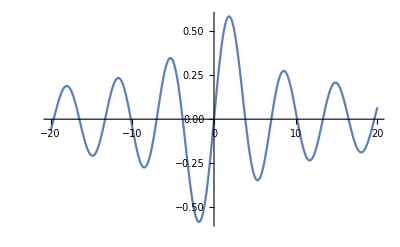

```mathematica
Plot[f[x], {x,-20,20}]
```

```mathematica
Solve[f[x]==0, x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→0}}

```mathematica
FindRoot[f[x]==0,{x,4}]
```

{x→3.83171}

```mathematica
FindRoot[f[x]==0,{x,7}]
```

{x→7.01559}

Q3: Integrate the expression f(x) = sin(x) e^-x, and then take it’s derivative.

```mathematica
f[x_] := Sin[x]*Exp[-x]
```

```mathematica
Integrate[f[x], x]
```

-1/2 ⅇ^-x (Cos[x]+Sin[x])

```mathematica
D[f[x], x]
```

ⅇ^-x Cos[x]-ⅇ^-x Sin[x]

```mathematica
g [x_] := Integrate[f[x], x]
```

```mathematica
D[g[x], x]
```

-1/2 ⅇ^-x (Cos[x]-Sin[x])+1/2 ⅇ^-x (Cos[x]+Sin[x])

```mathematica
Simplify[-1/2 ⅇ^-x (Cos[x]-Sin[x])+1/2 ⅇ^-x (Cos[x]+Sin[x])]
```

ⅇ^-x Sin[x]

Q4: Find the series expansion of the function f(x) = e^(-arctan(x)) about x=0, and about x → ∞. Hint: The arctan function is ArcTan[x].

```mathematica
f[x_]:= Exp[-ArcTan[x]]
```

```mathematica
Series[f[x], {x, 0, 5}]
```

1-x+x^2/2+x^3/6-(7 x^4)/24-x^5/24+O[x]^6

```mathematica
Series[f[x], {x, ∞, 5}]
```

ⅇ^(-π/2)+ⅇ^(-π/2)/x+ⅇ^(-π/2)/(2 x^2)-ⅇ^(-π/2)/(6 x^3)-(7 ⅇ^(-π/2))/(24 x^4)+ⅇ^(-π/2)/(24 x^5)+O[1/x]^6

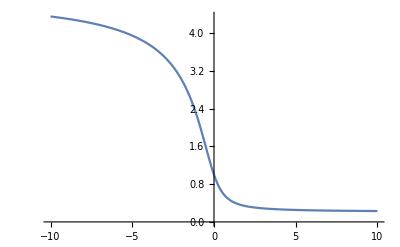

```mathematica
Plot[f[x], {x,-10,10}]
```

Q5: Solve the following differential equation using both DSolve and NDSolve (for x=-10 to x=10). Compare your answers by plotting them.
y’’(x) - x y(x) = 0
y(0) = 1
y’(0) = - 3^(1/3)Gamma(2/3)/Gamma(1/3)

```mathematica
DSolve[{y''[x]- x*y[x] == 0, y[0] == 1, y'[0] == -3 * Gamma[2/3] / Gamma[1/3]}, y[x], x]
```

{{y[x]→1/2 (3 3^(1/3) AiryAi[x] Gamma[2/3]+3^(2/3) AiryAi[x] Gamma[2/3]+3^(1/6) AiryBi[x] Gamma[2/3]-3^(5/6) AiryBi[x] Gamma[2/3])}}

```mathematica
NDSolve[{y''[x]- x*y[x] == 0,  y[0] == 1,y'[0] == -3 * Gamma[2/3] / Gamma[1/3]}, y[x], {x,-10,10}]
```

{{y[x]→InterpolatingFunction[…][x]}}

```mathematica
Plot[[x],x⟦InterpolatingFunction[{{-10.,10.}},{5,7,2,{347},{4},0,0,0,0,Automatic,{},{},False},{{-10.,-9.98115018863944,-9.962300377278877,-9.92655942018821,-9.886831692676784,-9.84710396516536,-9.807376237653934,-9.767648510142509,-9.727920782631083,-9.682071525255354,-9.636222267879626,-9.590373010503898,-9.544523753128168,-9.49867449575244,-9.452825238376711,-9.406975981000983,-9.361126723625253,-9.310685177684269,-9.260243631743284,-9.209802085802298,-9.159360539861314,-9.108918993920328,-9.058477447979344,-9.00803590203836,-8.957594356097374,-8.90715281015639,-8.85560855848792,-8.80406430681945,-8.752520055150981,-8.700975803482512,-8.649431551814041,-8.597887300145572,-8.546343048477103,-8.494798796808633,-8.443254545140164,-8.397556805228758,-8.351859065317353,-8.306161325405947,-8.260463585494541,-8.214765845583136,-8.169068105671728,-8.123370365760323,-8.077672625848917,-8.041400951597097,-8.005129277345276,-7.968857603093455,-7.932585928841634,-7.896314254589814,-7.860042580337994,-7.823770906086173,-7.776573239525376,-7.72937557296458,-7.682177906403784,-7.634980239842988,-7.587782573282191,-7.540584906721396,-7.493387240160599,-7.446189573599803,-7.388014824630486,-7.329840075661168,-7.27166532669185,-7.213490577722532,-7.155315828753215,-7.097141079783897,-7.03896633081458,-6.980791581845262,-6.939127446648985,-6.897463311452709,-6.855799176256433,-6.814135041060156,-6.772470905863879,-6.730806770667603,-6.689142635471327,-6.64747850027505,-6.596161387774325,-6.5448442752736,-6.493527162772875,-6.442210050272149,-6.390892937771424,-6.339575825270699,-6.288258712769974,-6.2369416002692475,-6.1739896383521495,-6.111037676435052,-6.048085714517953,-5.985133752600855,-5.922181790683757,-5.859229828766658,-5.79627786684956,-5.733325904932462,-5.670373943015363,-5.607421981098265,-5.544470019181167,-5.4815180572640685,-5.4185660953469705,-5.355614133429873,-5.292662171512774,-5.229710209595676,-5.166758247678578,-5.103806285761479,-5.040854323844381,-4.977902361927283,-4.914950400010184,-4.851998438093086,-4.789046476175988,-4.71250552961744,-4.635964583058892,-4.559423636500345,-4.482882689941797,-4.4063417433832495,-4.329800796824702,-4.253259850266154,-4.176718903707607,-4.100177957149059,-4.023637010590511,-3.9470960640319634,-3.8705551174734154,-3.794014170914868,-3.71747322435632,-3.6409322777977726,-3.564391331239225,-3.487850384680677,-3.4113094381221294,-3.334768491563582,-3.258227545005034,-3.1816865984464866,-3.1051456518879386,-3.021638613357664,-2.9381315748273895,-2.8546245362971145,-2.77111749776684,-2.6876104592365655,-2.604103420706291,-2.520596382176016,-2.4370893436457415,-2.353582305115467,-2.2700752665851924,-2.1865682280549175,-2.103061189524643,-2.0195541509943684,-1.9360471124640937,-1.852540073933819,-1.7690330354035444,-1.6855259968732696,-1.6217514764204617,-1.5579769559676537,-1.494202435514846,-1.430427915062038,-1.36665339460923,-1.3028788741564221,-1.2391043537036142,-1.1625199230203966,-1.085935492337179,-1.0093510616539614,-0.9327666309707436,-0.856182200287526,-0.7795977696043084,-0.7030133389210907,-0.6264289082378731,-0.5498444775546555,-0.4732600468714378,-0.4231219989984459,-0.37298395112545396,-0.32284590325246204,-0.2727078553794702,-0.22256980750647823,-0.17243175963348634,-0.1494305913461917,-0.12642942305889704,-0.10342825477160242,-0.08042708648430778,-0.05742591819701315,-0.04592533405336583,-0.03442474990971851,-0.022924165766071196,-0.011423581622423877,-0.007741198359847167,-0.004058815097270458,-0.0003764318346937475,-0.00018821591734687374,0.,0.00018821591734687374,0.0003764318346937475,0.004059072311392652,0.007741712788091556,0.01142435326479046,0.023019580657774055,0.03461480805075765,0.04621003544374125,0.05780526283672484,0.08099571762269203,0.10418617240865923,0.12737662719462642,0.1505670819805936,0.1737575367665608,0.224384370138324,0.27501120351008723,0.3256380368818504,0.3762648702536136,0.4268917036253768,0.47751853699714003,0.5475308689723096,0.6175432009474792,0.6875555329226487,0.7575678648978184,0.8275801968729879,0.8975925288481574,0.967604860823327,1.052877883817909,1.1381509068124906,1.2234239298070726,1.3086969528016545,1.3939699757962363,1.4792429987908182,1.5645160217854,1.649789044779982,1.7350620677745638,1.8203350907691456,1.9056081137637275,1.9908811367583095,2.076154159752891,2.161427182747473,2.246700205742055,2.331973228736637,2.4172462517312185,2.5025192747258007,2.5877922977203824,2.673065320714964,2.7583383437095463,2.843611366704128,2.92888438969871,3.014157412693292,3.0994304356878737,3.1847034586824554,3.2699764816770376,3.3552495046716193,3.440522527666201,3.511231499482907,3.5819404712996126,3.6526494431163186,3.723358414933024,3.79406738674973,3.864776358566436,3.9354853303831416,4.006194302199847,4.076903274016553,4.147612245833259,4.218321217649965,4.28903018946667,4.359739161283376,4.430448133100082,4.501157104916788,4.571866076733494,4.642575048550199,4.713284020366905,4.783992992183611,4.854701964000317,4.925410935817022,4.996119907633728,5.066828879450434,5.13753785126714,5.208246823083846,5.2789557949005514,5.349664766717257,5.420373738533963,5.491082710350669,5.5617916821673745,5.6325006539840805,5.7032096258007865,5.7739185976174925,5.832751195087881,5.8915837925582695,5.950416390028658,6.009248987499046,6.068081584969434,6.1269141824398226,6.185746779910211,6.2445793773805995,6.303411974850988,6.3622445723213765,6.421077169791765,6.4799097672621535,6.538742364732541,6.59757496220293,6.656407559673318,6.715240157143707,6.774072754614095,6.832905352084484,6.891737949554872,6.950570547025261,7.009403144495649,7.068235741966037,7.127068339436425,7.185900936906814,7.244733534377202,7.303566131847591,7.362398729317979,7.421231326788368,7.480063924258756,7.538896521729145,7.597729119199532,7.656561716669921,7.715394314140309,7.774226911610698,7.833059509081086,7.891892106551475,7.950724704021863,8.00955730149225,8.06838989896264,8.127222496433028,8.186055093903416,8.244887691373805,8.303720288844193,8.362552886314582,8.42138548378497,8.480218081255359,8.539050678725747,8.597883276196136,8.656715873666524,8.715548471136913,8.774381068607301,8.83321366607769,8.892046263548078,8.950878861018465,9.009711458488853,9.068544055959242,9.117497219506118,9.166450383052993,9.215403546599868,9.264356710146743,9.313309873693617,9.362263037240492,9.411216200787369,9.460169364334243,9.509122527881118,9.558075691427993,9.607028854974867,9.655982018521744,9.704935182068619,9.753888345615493,9.802841509162368,9.851794672709243,9.900747836256118,9.949700999802994,9.974850499901496,9.987425249950748,10.}},{Developer`PackedArrayForm,{0,3,6,9,12,15,18,21,24,27,30,33,36,39,42,45,48,51,54,57,60,63,66,69,72,75,78,81,84,87,90,93,96,99,102,105,108,111,114,117,120,123,126,129,132,135,138,141,144,147,150,153,156,159,162,165,168,171,174,177,180,183,186,189,192,195,198,201,204,207,210,213,216,219,222,225,228,231,234,237,240,243,246,249,252,255,258,261,264,267,270,273,276,279,282,285,288,291,294,297,300,303,306,309,312,315,318,321,324,327,330,333,336,339,342,345,348,351,354,357,360,363,366,369,372,375,378,381,384,387,390,393,396,399,402,405,408,411,414,417,420,423,426,429,432,435,438,441,444,447,450,453,456,459,462,465,468,471,474,477,480,483,486,489,492,495,498,501,504,507,510,513,516,519,522,525,528,531,534,537,540,543,546,549,552,555,558,561,564,567,570,573,576,579,582,585,588,591,594,597,600,603,606,609,612,615,618,621,624,627,630,633,636,639,642,645,648,651,654,657,660,663,666,669,672,675,678,681,684,687,690,693,696,699,702,705,708,711,714,717,720,723,726,729,732,735,738,741,744,747,750,753,756,759,762,765,768,771,774,777,780,783,786,789,792,795,798,801,804,807,810,813,816,819,822,825,828,831,834,837,840,843,846,849,852,855,858,861,864,867,870,873,876,879,882,885,888,891,894,897,900,903,906,909,912,915,918,921,924,927,930,933,936,939,942,945,948,951,954,957,960,963,966,969,972,975,978,981,984,987,990,993,996,999,1002,1005,1008,1011,1014,1017,1020,1023,1026,1029,1032,1035,1038,1041},{0.4509176067084455,4.216729412053581,-4.509176067113057,0.5295547935375552,4.124382916385565,-5.285565927429456,0.6063145792833753,4.017601735918846,-6.040287963658921,0.7457544003053249,3.7770834047390713,-7.402775366673604,0.8895921307557684,3.454870295535175,-8.795247673042855,1.0195678626664153,3.0802131282933964,-10.039790737799924,1.1337196588002827,2.6593473108426715,-11.118815242842338,1.2303464402813125,2.1991508974771383,-12.017591565204235,1.3080312167221844,1.7070273324942358,-12.724424036200777,1.3727006484160065,1.1096041988606211,-13.29058583643689,1.409479387796372,0.49250142147062154,-13.58205663603695,1.4177550742380798,-0.13161807312456883,-13.59679997148598,1.3974960793673374,-0.7501282002013322,-13.338434502136327,1.3492439358628936,-1.3506947211450737,-12.816028952052827,1.2740943283731188,-1.9215183823737496,-12.043791020464083,1.173667297845498,-2.451561540678935,-11.040660078195206,1.0500675151746275,-2.9307541232989127,-9.829815073072613,0.8903622248566387,-3.388585790121787,-8.289882363934506,0.7096025350477944,-3.764053899803734,-6.5710923495422895,0.5121524393340473,-4.04921869050225,-4.716822596552672,0.3027201566627219,-4.23839052744685,-2.7727230499853817,0.08624222542112615,-4.328215728950733,-0.7855734368691184,-0.13223528096929846,-4.31770486885865,1.1978503180308275,-0.34767553415524954,-4.208204696060984,3.131873702317907,-0.5551669440907332,-4.0033161276344265,4.972960292238361,-0.7500337270828423,-3.7087619618752,6.6806650297949135,-0.9316080762349164,-3.3231291012477895,8.24995645881549,-1.0913107002741769,-2.8619196642682554,9.607969593050202,-1.225539853293522,-2.3367750768579105,10.726562148573692,-1.331328494539207,-1.7606276807791037,11.583857034329421,-1.4064023382891602,-1.1473683643148562,12.164580779244426,-1.4492203937573556,-0.5115010636225158,12.460233637686155,-1.4589975470088028,0.13220716890830086,12.469093523488622,-1.435709170270036,0.7690721880365458,12.196060504521391,-1.3800781717129476,1.384826817185762,11.652351280776681,-1.3048530503586178,1.9021702625193688,10.95757759488513,-1.2067774420876038,2.383496064183097,10.078835107264462,-1.0876832134785899,2.820806116492492,9.034472218737791,-0.9497476555689979,3.20699995183697,7.845355888745485,-0.7954499803829463,3.5359799529820855,6.534435285572227,-0.6275234814389812,3.8027360950108267,5.126282080619796,-0.44890430447359236,4.003409272797694,3.646615948877736,-0.2626778256785214,4.135332850521122,2.121825492643782,-0.11155486581472482,4.190098083402361,0.8970574159194139,0.04074846128453714,4.200426813627709,-0.3261966875611621,0.19262422021210937,4.166609627339434,-1.5349949696690566,0.34248345190319307,4.089399968299654,-2.716779404329342,0.48877268187413514,3.969997888054214,-3.8595026946338415,0.629989756321772,3.810029351964702,-4.9517463093742995,0.7646988544601054,3.611521442655068,-5.982828648643131,0.928020324870291,3.2995126218287467,-7.2168180174809144,1.0752913877040264,2.932483347606913,-8.311330982926272,1.2040769372563784,2.517416274722182,-9.249933233740565,1.312288599872931,2.061997075151712,-10.01929752808156,1.3982143960119684,1.574464185694966,-10.609346804207561,1.4605411730340594,1.0634532327597024,-11.013334733235048,1.4983696284669066,0.5378392037371162,-11.227863826663226,1.5112218922236518,0.006579055110240727,-11.252844623823801,1.4926508081888885,-0.6428528145635888,-11.027726226561116,1.4368350515578263,-1.2712351669104993,-10.531771073467699,1.34544780900008,-1.8633253526268667,-9.783646117661835,1.2210140617641025,-2.405137867520016,-8.807773371157202,1.0668281690098296,-2.8842552935275365,-7.633492433329415,0.8868548379455695,-3.2900877858449933,-6.294133862963977,0.6856165986484519,-3.614076761648875,-4.826032144169242,0.4680711282496827,-3.8498401040848367,-3.2675069899126394,0.3051661204004525,-3.96208863764733,-2.117586600679235,0.1385868946341762,-4.026131583626854,-0.9558980197585263,-0.02965203915161704,-4.041776884427101,0.20328842588066776,-0.19754046187898813,-4.0094200223533205,1.3460673846593323,-0.36309655947018726,-3.9300253930600246,2.4590608839739514,-0.5243901249918945,-3.805101153479318,3.529568605149789,-0.6795645832037005,-3.6366680995419594,4.545704425524439,-0.8268576104956684,-3.427223144541591,5.49651818491911,-0.9950138102976466,-3.1172619718868435,6.5632716673310565,-1.1459145903489685,-2.755835481612153,7.499832541157145,-1.27709649764814,-2.3499793807449088,8.292860784876085,-1.38647341863013,-1.9073390534757997,8.931952988848192,-1.472363960726617,-1.43601662205675,9.409720415828124,-1.5335109039833246,-0.9444154672308324,9.721808660770227,-1.5690926774332743,-0.44108526862009256,9.86686067346194,-1.5787269542914544,0.06542980861149617,9.846427752052037,-1.5552199023195463,0.6788273873426276,9.601911501517955,-1.4937367131014436,1.269536708210237,9.128281276836447,-1.3961482419403124,1.8236908251724215,8.444024188196162,-1.2651585550671722,2.328732750423698,7.572143128115069,-1.1042140352330305,2.7736748749022353,6.539356217958582,-0.9173977809810694,3.149306222102687,5.37524441639407,-0.7093126694036576,3.448345095764814,4.111373307483141,-0.484956553826055,3.665536285965408,2.780413961439664,-0.24959307367345673,3.7976935168942134,1.4152860571380217,-0.008621463998205266,3.843689207842841,0.04834418910239451,0.23255141478518848,3.804394858261158,-1.289374339158244,0.4686338538764253,3.682576424448762,-2.568824918876657,0.6945642032419841,3.48274992477556,-3.7635420258351906,0.9056155936368081,3.2110031758407067,-4.8501276513977425,1.097488532033835,2.8747900219252815,-5.808636015842344,1.2663898573633239,2.4827036912534353,-6.622851939422713,1.4090969387774575,2.0442359664508882,-7.280463208081327,1.5230064519621331,1.569528784309447,-7.7731298738600625,1.6061674309078233,1.069124553080198,-8.096456023134213,1.6572987389004636,0.5537211706896557,-8.249871266051425,1.6757913810762237,0.0339370395621349,-8.236431521960219,1.6616965008805278,-0.4799089986914376,-8.062548783255135,1.615700057098433,-0.9779989657806365,-7.737662577175808,1.518697264110524,-1.5492505435375024,-7.156869185694547,1.3798533814257181,-2.0690126902339996,-6.396951355558573,1.203605802322102,-2.524696945359315,-5.487748711553758,0.9952652598173573,-2.90610418173282,-4.461657389327877,0.760826604569605,-3.2055753679010124,-3.352462026320652,0.5067714229023209,-3.4180546807342647,-2.194219322836076,0.23986901991430656,-3.541070181150175,-1.0202252944595325,-0.03301819464056683,-3.574639498009494,0.13790768650621318,-0.3051195203271303,-3.521109719722391,1.2510442944239677,-0.5699263379819475,-3.3849419652506194,2.2931766656523807,-0.8213442331639581,-3.1724518939269277,3.241924547143627,-1.0538239410037713,-2.8915177528282725,4.078883604635006,-1.2624690712462032,-2.5512674735969134,4.789825505257033,-1.4431194355764294,-2.1617558853997623,5.3647578222739405,-1.5924096231809888,-1.7336423389525366,5.797855561354037,-1.7078032145348572,-1.2778780283099,6.0872789422211415,-1.787603698656478,-0.8054110794682131,6.234894221807344,-1.8309437117886325,-0.3269161502156449,6.245915543397851,-1.8377546995280785,0.14744613141252289,6.128486449598311,-1.8087194267612605,0.6082359739320304,5.893219447155024,-1.745210050034674,1.0469049530468986,5.552711417582945,-1.6492145459102714,1.4559290625564827,5.121051370154909,-1.5104025778836672,1.8608692506025817,4.563890752491707,-1.3398054588983956,2.216208751906378,3.9365247305536064,-1.1417861960889821,2.5169388836446616,3.2593709028689384,-0.9210552778673146,2.75973922489682,2.5523524126684514,-0.682532042522407,2.9429141214123464,1.8343802739939894,-0.4312130535037742,3.066289586321206,1.1229234066683376,-0.17205047825941683,3.131078090044234,0.43366983180814306,0.0901571673243123,3.1397188737186905,-0.21972105332703318,0.3508601788934342,3.0957012758711144,-0.8257782919350871,0.6058376107301824,3.003378196775059,-1.3752969597081763,0.8512614638597787,2.867776248960607,-1.861341258308433,1.083745088923764,2.6944084531755133,-2.279182220821178,1.3003762326811072,2.4890945050430195,-2.626180198859182,1.498735535672781,2.2577928157423672,-2.9016225856374356,1.676901621641246,2.006447573156558,-3.1065274633918314,1.833444131124941,1.7408532905101972,-3.2434232449537213,1.9674062304216677,1.466538377511363,-3.316114350805819,2.0541743663836742,1.2543908805351616,-3.331360314631257,2.1274041318534143,1.0423103628641723,-3.31444661682808,2.1871634047791826,0.8322629312117396,-3.2680648890936426,2.2336398628875958,0.626037825210344,-3.1950608164270093,2.2671294283730687,0.42523933702593336,-3.0983801302135636,2.28802430424549,0.23128204143753647,-2.9810185349285674,2.2968008027602194,0.045389116180637366,-2.8459758850903927,2.2921035067919404,-0.16574301792863863,-2.6646160016918934,2.2717857027894177,-0.3623326456668842,-2.467012733664645,2.2370040423875572,-0.5433195837865561,-2.257922411825156,2.188982693650623,-0.7079971063952136,-2.0418100176997283,2.128987176647639,-0.8559876953995672,-1.8228009298193708,2.058300184138187,-0.9872156193939696,-1.6046462393603198,1.9781995924817928,-1.1018773505704786,-1.3907007109512772,1.8899387952886086,-1.200410743865688,-1.1839122921035117,1.7947293997016143,-1.2834638076469225,-0.9868220455427776,1.6937262902259282,-1.3518637657321915,-0.8015729829173888,1.6249873681413558,-1.3891697742797546,-0.6875679030073888,1.554518712390528,-1.420914834044703,-0.5798105311192032,1.4825911331566552,-1.4474211609865013,-0.4786484744431714,1.4094588742564846,-1.4690269102980746,-0.384370506002653,1.335358884878574,-1.4860833348089189,-0.29721056931201206,1.260510228278594,-1.4989520695546854,-0.21735199667686958,1.2259781300460788,-1.5035556225580047,-0.18319863693299102,1.1913490404352718,-1.5073917188656014,-0.1506215718334947,1.1566401940900732,-1.5104967158302602,-0.11962927666621206,1.1218679814047092,-1.5129071468734416,-0.09022857315778847,1.0870479684766245,-1.5146596833287667,-0.062424727713622036,1.0696246667244171,-1.5153007307332065,-0.049122870130846125,1.0521948634007978,-1.515791101931059,-0.0362215449780142,1.0347602648168728,-1.516135404871565,-0.023721015872596892,1.0173225039511382,-1.5163381885297915,-0.011621466661806997,1.011738699638063,-1.5163740062186246,-0.007832069963311289,1.006154788983131,-1.5163959456117724,-0.004083796248013089,1.0005708228127292,-1.5164041581420196,-0.0003766467105749403,1.000285411413036,-1.5164042290329256,-0.0001882696363190549,1.,-1.5164042644682678,0.,0.99971458858696,-1.516404229053147,0.0001881621983746926,0.9994291771872477,-1.516404158243127,0.0003762169588125503,0.9938448208080304,-1.5163960374593595,0.0040340879942603524,0.9882605189990225,-1.5163745217850322,0.007650829098980312,0.9826763208098951,-1.5163397626847523,0.011226441435469888,0.9650949977157842,-1.5161454193216064,0.022216082177111934,0.9475166774711418,-1.515826074434156,0.03279810786315296,0.9299427622857055,-1.5153863909282557,0.042972688005689125,0.9123746201880669,-1.5148310919423837,0.052740054725213224,0.8772608580140091,-1.5133925240322745,0.07105437273148195,0.8421852419804877,-1.5115480836583561,0.08774405681686001,0.8071567357414076,-1.5093354037186435,0.10281290261150103,0.7721834495746012,-1.5067920215908002,0.11626540874815273,0.7372726184242707,-1.5039553628647246,0.12810667409494828,0.6613057733598305,-1.4969242161845016,0.14838667925483065,0.585717631569556,-1.4890587259071515,0.16107891089322052,0.5105407413417811,-1.4807413005490142,0.16625148576364407,0.4357883745086992,-1.4723509207571197,0.1639718568299091,0.3614547011780393,-1.4642632665201456,0.15430201380744885,0.28751494796525817,-1.456851117560706,0.1372937180255586,0.18582769427326778,-1.4484019536112114,0.10174640188396325,0.08463348595351858,-1.442929227900002,0.05226483672463658,-0.016310248707093487,-1.4414101374026416,-0.011214206921116522,-0.11731474295193821,-1.4448303148386954,-0.08887388120143407,-0.21876079541703766,-1.4541931337930647,-0.18104210195717452,-0.3211003929046237,-1.470530747640692,-0.2882173132562452,-0.42485916294281606,-1.494916967199205,-0.411095790455604,-0.5540308715330011,-1.5371333067963255,-0.5833268490758097,-0.6874604929020682,-1.5951643592234275,-0.7824337794568178,-0.826597570132062,-1.6714188584657734,-1.0112792473650298,-0.9731083546152938,-1.7685819657961068,-1.2735039370089323,-1.1289023594469962,-1.8896869862993488,-1.5736559909774963,-1.2961655298693056,-2.0381990843218336,-1.9173437803889772,-1.4774011321411848,-2.218113214012531,-2.311417735447619,-1.675479698405988,-2.4340690338687923,-2.764188043185459,-1.8936996122718899,-2.6914861975331146,-3.285686354966128,-2.1358602445093617,-2.996724180257729,-3.8879813393450067,-2.406349941063824,-3.357271723366062,-4.585559956193546,-2.7102516438010182,-3.781972094451592,-5.395788853196924,-3.053469510016336,-4.281291718176232,-6.3394733991602354,-3.4428806085404156,-4.867641383423775,-7.4415357016238275,-3.8865166383563565,-5.555761247612149,-8.731837689615025,-4.393781674136461,-6.363183323446522,-10.246181184447641,-4.975713234330293,-7.3107881523157054,-12.027524098639747,-5.645295544453753,-8.423476073167087,-14.127460826746118,-6.417835795966871,-9.730978048282592,-16.608025933121557,-7.311416560233602,-11.268836609623987,-19.54389391555953,-8.347440407376919,-13.079594392286268,-23.0250647734586,-9.551286325072985,-15.21423623739849,-27.160146139315135,-10.953101886022658,-17.733941364888864,-32.08036885125847,-12.588760465678241,-20.712215122683766,-37.94450531609096,-14.501019400862724,-24.237485919942245,-44.9449004236906,-16.74092310025787,-28.416272906656772,-53.31487511853558,-19.36950513695217,-33.377054720265235,-63.337825520289435,-22.459855729787577,-39.27500037217221,-75.3584188703296,-26.099636326505944,-46.29776158654484,-89.796385544262,-29.60913878862839,-53.135256026789264,-103.96454012944548,-33.63942175746337,-61.055828513364375,-120.49440619705128,-38.27330214395866,-70.24066718600537,-139.79895503795754,-43.60750120122042,-80.90274407489724,-162.36635608546604,-49.755090823200064,-93.29261793263238,-188.7741667261247,-56.84838816940851,-107.7053370810005,-219.7063057087213,-65.04238373558552,-124.48865647874405,-255.97334602800416,-74.51880398823124,-144.05282601078005,-298.5368066328794,-85.49093087266267,-166.88226174911654,-348.5382543805459,-98.20932390492618,-193.54947305138498,-407.33419253364934,-112.96861973944817,-224.73169545692377,-476.5379231655068,-130.1156192209772,-261.23077165057833,-558.069816004784,-150.05891389208418,-303.9969341655575,-654.2177197561626,-173.28035490172894,-354.1572790958318,-767.7096203966262,-200.3487286587334,-413.04988407141263,-901.8010979465058,-231.93607776138444,-482.26472283295266,-1060.3806790884762,-268.8371955194851,-563.6927705114589,-1248.0968476582614,-311.9929309875494,-659.5849874098927,-1470.5112857509073,-362.5180729892927,-772.6232262593741,-1734.2839079589423,-421.7347410792186,-906.0055425525575,-2047.3964600462334,-491.21240480845796,-1063.548916834586,-2419.4229309838474,-572.8158874724681,-1249.8130428628492,-2861.8568347443593,-668.7629957725895,-1470.2496222052791,-3388.507630724288,-781.6937636259983,-1731.3825659407241,-4015.9812618963974,-914.75372030937,-2041.025676750948,-4764.263112103131,-1071.694106886493,-2408.545817943236,-5657.4257594168075,-1256.9925909006042,-2845.1813290216537,-6724.488905543708,-1475.998792711217,-3364.427593266433,-8000.465007279885,-1735.1098684618269,-3982.50429129022,-9527.631691512204,-2041.9825323924185,-4718.922096624025,-11357.081330002615,-2405.789291700001,-5597.170521951073,-13550.609592645927,-2837.528367821558,-6645.553476771614,-16183.018894256544,-3350.398859606237,-7898.205058099497,-19344.9300279877,-3850.276987805832,-9125.541827265075,-22457.7075622098,-4428.036559811,-10550.838848281093,-26088.14842154445,-5096.269036046332,-12207.08953894345,-30324.92265194475,-5869.669100217427,-14132.950459989042,-35272.3030018548,-6765.396340662037,-16373.739484496706,-41052.97681477943,-7803.500852871311,-18982.614473756545,-47811.37986951279,-9007.424337571716,-22021.96574772361,-55717.64589895992,-10404.590309034867,-25565.061753292834,-64972.28982922652,-12027.099738536166,-29697.995283544897,-75811.76422293342,-13912.551383992579,-34521.98623266404,-88515.05418117119,-16105.009684811295,-40156.107673483435,-103411.50958292447,-18656.147415716277,-46740.514836888404,-120890.15135008506,-21626.595380517625,-54440.27176375007,-141410.7348059908,-25087.537540803114,-63449.88868406383,-165516.90880206518,-29122.597244825323,-73998.70497696564,-193851.87556471492,-33830.06889635371,-86357.2786656848,-227177.0360933178,-39325.55976957423,-100844.97466440761,-266394.2016926179,-45745.119049900895,-117838.9814244059,-312572.0672142644,-53248.945971706926,-137785.03049334048,-366977.7798249337,-62025.786609615156,-161210.14729514447,-431114.60326484183,-72298.15003483399,-188737.82596502296,-506766.87741296226,-84328.4998688041,-221106.09851935125,-596053.7134716575,-98426.60758609847,-259189.06163054606,-701493.1546079852,-114958.29024261936,-304022.5359877827,-826078.880621376,-134355.7988446085,-356834.667489561,-973371.9554436592,-157130.1757871589,-419082.4409639652,-1.147610622916376*^6,-183885.9624369301,-492495.2713448594,-1.3538417673878015*^6,-215338.71313401303,-579127.071015659,-1.5980783931071018*^6,-252335.86220241332,-681418.4735548766,-1.8874883667021366*^6,-295881.5990783866,-802271.2332899811,-2.2306207424050537*^6,-347166.5371242317,-945137.228888558,-2.637677289211281*^6,-407603.11860381,-1.1141249922259217*^6,-3.120838410274245*^6,-478867.8871096821,-1.314127278585594*^6,-3.6946545451962836*^6,-562951.986048149,-1.5509739122375047*^6,-4.376516445539214*^6,-662221.5155919662,-1.8316150085149112*^6,-5.187220498039579*^6,-779489.7104676361,-2.1643407211282034*^6,-6.15164864231095*^6,-918103.2987637367,-2.5590449298022534*^6,-7.299586516378458*^6,-1.082045881817653*^6,-3.0275418147951392*^6,-8.666708417791318*^6,-1.2760617543627152*^6,-3.5839461178288846*^6,-1.0295763677366057*^7,-1.5058042833616226*^6,-4.245130131985204*^6,-1.2238006334798357*^7,-1.7780138086354153*^6,-5.031273179571994*^6,-1.4554918858387442*^7,-2.1007310492603984*^6,-5.966522628318986*^6,-1.732029140395973*^7,-2.4835532340860087*^6,-7.079789486051222*^6,-2.062273117445011*^7,-2.9379416679962794*^6,-8.405706452690002*^6,-2.4568692326541297*^7,-3.4775912528560413*^6,-9.985782179406477*^6,-2.9286136191105906*^7,-4.118874670540302*^6,-1.186979261154712*^7,-3.4928955083643526*^7,-4.8813765866791895*^6,-1.4117458947213557*^7,-4.1682321600799575*^7,-5.788536447147174*^6,-1.6800472259805888*^7,-4.976916015616411*^7,-6.868422335930794*^6,-2.000493761656972*^7,-5.9457979981480345*^7,-8.154663090320125*^6,-2.383432607224693*^7,-7.107236059560393*^7,-9.687571607192168*^6,-2.84130418333882*^7,-8.500244388946281*^7,-1.1515499241783317*^7,-3.3890734915599085*^7,-1.0171886402245353*^8,-1.3696469665357698*^7,-4.044751765898666*^7,-1.2178964037698746*^8,-1.6300150837200867*^7,-4.83002776348574*^7,-1.459006736778637*^8,-1.9410236258309446*^7,-5.77103211261317*^7,-1.7488062571893087*^8,-2.3127321896396123*^7,-6.899263215653016*^7,-2.0973113467881927*^8,-2.676921948671562*^7,-8.007851285709141*^7,-2.4406828271271935*^8,-3.0997148042583846*^7,-9.298185838876733*^7,-2.8413381947991395*^8,-3.5907314845491014*^7,-1.0800626686001675*^8,-3.309003949951654*^8,-4.161201943691813*^7,-1.2550695164546712*^8,-3.855085904836143*^8,-4.82423924573764*^7,-1.458996615455214*^8,-4.4929634861433905*^8,-5.59516087352172*^7,-1.6967116837194675*^8,-5.238336764857845*^8,-6.491865804108867*^7,-1.973916010246485*^8,-6.109635243440087*^8,-7.535277101240677*^7,-2.297289535405868*^8,-7.12849973394467*^8,-8.749861656325683*^7,-2.6746615838165793*^8,-8.320350630247852*^8,-1.0164240704781917*^8,-3.115211840908045*^8,-9.715058166111052*^8,-1.1811907213411826*^8,-3.629707009793955*^8,-1.1347733302167923*^9,-1.3732069147878587*^8,-4.2307795794857043*^8,-1.3259661228326042*^9,-1.597064103347413*^8,-4.933256303079725*^8,-1.549940354672336*^9,-1.8581410286917785*^8,-5.754545380029396*^8,-1.8124100055279734*^9,-2.1627409589311764*^8,-6.715092984705824*^8,-2.1201006763645375*^9,-2.5182532241911098*^8,-7.838921738580624*^8,-2.480931360070711*^9,-2.9333434168854403*^8,-9.154266044228091*^8,-2.90422933710063*^9,-3.418177418621684*^8,-1.0694321951387897*^9,-3.4009843140393925*^9,-3.698187090064405*^8,-1.1585358101151576*^9,-3.688886333429397*^9,-3.846826521648393*^8,-1.205878631719584*^9,-3.841989233581137*^9,-4.001541918628005*^8,-1.2551869519794009*^9,-4.0015419182208714*^9}},{Automatic}][x],1,1⟧]
```

Part::pkspec1: The expression InterpolatingFunction[{{-10.,10.}},{5,7,2,{347},{4},0,0,0,0,Automatic,«3»},{{-10.,-9.98115,-9.9623,-9.92656,-9.88683,-«17»,-«18»,-9.76765,-9.72792,-9.68207,«337»}},{Developer`PackedArrayForm,{0,3,6,9,12,15,18,21,24,27,«338»},{0.450918,4.21673,-4.50918,0.529555,4.12438,-5.28557,0.606315,4.0176,-6.04029,0.745754,«1031»}},{Automatic}][x] cannot be used as a part specification.

Plot::pllim: Range specification x⟦«1»,1,1⟧ is not of the form {x, xmin, xmax}.

Plot[InterpolatingFunction[{{-10.,10.}},{5,7,2,{347},{4},0,0,0,0,Automatic,{},{},False},{{-10.,-9.98115,-9.9623,-9.92656,-9.88683,-9.8471,-9.80738,-9.76765,-9.72792,-9.68207,-9.63622,-9.59037,-9.54452,-9.49867,-9.45283,-9.40698,-9.36113,-9.31069,-9.26024,-9.2098,-9.15936,-9.10892,-9.05848,-9.00804,-8.95759,-8.90715,-8.85561,-8.80406,-8.75252,-8.70098,-8.64943,-8.59789,-8.54634,-8.4948,-8.44325,-8.39756,-8.35186,-8.30616,-8.26046,-8.21477,-8.16907,-8.12337,-8.07767,-8.0414,-8.00513,-7.96886,-7.93259,-7.89631,-7.86004,-7.82377,-7.77657,-7.72938,-7.68218,-7.63498,-7.58778,-7.54058,-7.49339,-7.44619,-7.38801,-7.32984,-7.27167,-7.21349,-7.15532,-7.09714,-7.03897,-6.98079,-6.93913,-6.89746,-6.8558,-6.81414,-6.77247,-6.73081,-6.68914,-6.64748,-6.59616,-6.54484,-6.49353,-6.44221,-6.39089,-6.33958,-6.28826,-6.23694,-6.17399,-6.11104,-6.04809,-5.98513,-5.92218,-5.85923,-5.79628,-5.73333,-5.67037,-5.60742,-5.54447,-5.48152,-5.41857,-5.35561,-5.29266,-5.22971,-5.16676,-5.10381,-5.04085,-4.9779,-4.91495,-4.852,-4.78905,-4.71251,-4.63596,-4.55942,-4.48288,-4.40634,-4.3298,-4.25326,-4.17672,-4.10018,-4.02364,-3.9471,-3.87056,-3.79401,-3.71747,-3.64093,-3.56439,-3.48785,-3.41131,-3.33477,-3.25823,-3.18169,-3.10515,-3.02164,-2.93813,-2.85462,-2.77112,-2.68761,-2.6041,-2.5206,-2.43709,-2.35358,-2.27008,-2.18657,-2.10306,-2.01955,-1.93605,-1.85254,-1.76903,-1.68553,-1.62175,-1.55798,-1.4942,-1.43043,-1.36665,-1.30288,-1.2391,-1.16252,-1.08594,-1.00935,-0.932767,-0.856182,-0.779598,-0.703013,-0.626429,-0.549844,-0.47326,-0.423122,-0.372984,-0.322846,-0.272708,-0.22257,-0.172432,-0.149431,-0.126429,-0.103428,-0.0804271,-0.0574259,-0.0459253,-0.0344247,-0.0229242,-0.0114236,-0.0077412,-0.00405882,-0.000376432,-0.000188216,0.,0.000188216,0.000376432,0.00405907,0.00774171,0.0114244,0.0230196,0.0346148,0.04621,0.0578053,0.0809957,0.104186,0.127377,0.150567,0.173758,0.224384,0.275011,0.325638,0.376265,0.426892,0.477519,0.547531,0.617543,0.687556,0.757568,0.82758,0.897593,0.967605,1.05288,1.13815,1.22342,1.3087,1.39397,1.47924,1.56452,1.64979,1.73506,1.82034,1.90561,1.99088,2.07615,2.16143,2.2467,2.33197,2.41725,2.50252,2.58779,2.67307,2.75834,2.84361,2.92888,3.01416,3.09943,3.1847,3.26998,3.35525,3.44052,3.51123,3.58194,3.65265,3.72336,3.79407,3.86478,3.93549,4.00619,4.0769,4.14761,4.21832,4.28903,4.35974,4.43045,4.50116,4.57187,4.64258,4.71328,4.78399,4.8547,4.92541,4.99612,5.06683,5.13754,5.20825,5.27896,5.34966,5.42037,5.49108,5.56179,5.6325,5.70321,5.77392,5.83275,5.89158,5.95042,6.00925,6.06808,6.12691,6.18575,6.24458,6.30341,6.36224,6.42108,6.47991,6.53874,6.59757,6.65641,6.71524,6.77407,6.83291,6.89174,6.95057,7.0094,7.06824,7.12707,7.1859,7.24473,7.30357,7.3624,7.42123,7.48006,7.5389,7.59773,7.65656,7.71539,7.77423,7.83306,7.89189,7.95072,8.00956,8.06839,8.12722,8.18606,8.24489,8.30372,8.36255,8.42139,8.48022,8.53905,8.59788,8.65672,8.71555,8.77438,8.83321,8.89205,8.95088,9.00971,9.06854,9.1175,9.16645,9.2154,9.26436,9.31331,9.36226,9.41122,9.46017,9.50912,9.55808,9.60703,9.65598,9.70494,9.75389,9.80284,9.85179,9.90075,9.9497,9.97485,9.98743,10.}},{Developer`PackedArrayForm,{0,3,6,9,12,15,18,21,24,27,30,33,36,39,42,45,48,51,54,57,60,63,66,69,72,75,78,81,84,87,90,93,96,99,102,105,108,111,114,117,120,123,126,129,132,135,138,141,144,147,150,153,156,159,162,165,168,171,174,177,180,183,186,189,192,195,198,201,204,207,210,213,216,219,222,225,228,231,234,237,240,243,246,249,252,255,258,261,264,267,270,273,276,279,282,285,288,291,294,297,300,303,306,309,312,315,318,321,324,327,330,333,336,339,342,345,348,351,354,357,360,363,366,369,372,375,378,381,384,387,390,393,396,399,402,405,408,411,414,417,420,423,426,429,432,435,438,441,444,447,450,453,456,459,462,465,468,471,474,477,480,483,486,489,492,495,498,501,504,507,510,513,516,519,522,525,528,531,534,537,540,543,546,549,552,555,558,561,564,567,570,573,576,579,582,585,588,591,594,597,600,603,606,609,612,615,618,621,624,627,630,633,636,639,642,645,648,651,654,657,660,663,666,669,672,675,678,681,684,687,690,693,696,699,702,705,708,711,714,717,720,723,726,729,732,735,738,741,744,747,750,753,756,759,762,765,768,771,774,777,780,783,786,789,792,795,798,801,804,807,810,813,816,819,822,825,828,831,834,837,840,843,846,849,852,855,858,861,864,867,870,873,876,879,882,885,888,891,894,897,900,903,906,909,912,915,918,921,924,927,930,933,936,939,942,945,948,951,954,957,960,963,966,969,972,975,978,981,984,987,990,993,996,999,1002,1005,1008,1011,1014,1017,1020,1023,1026,1029,1032,1035,1038,1041},{0.450918,4.21673,-4.50918,0.529555,4.12438,-5.28557,0.606315,4.0176,-6.04029,0.745754,3.77708,-7.40278,0.889592,3.45487,-8.79525,1.01957,3.08021,-10.0398,1.13372,2.65935,-11.1188,1.23035,2.19915,-12.0176,1.30803,1.70703,-12.7244,1.3727,1.1096,-13.2906,1.40948,0.492501,-13.5821,1.41776,-0.131618,-13.5968,1.3975,-0.750128,-13.3384,1.34924,-1.35069,-12.816,1.27409,-1.92152,-12.0438,1.17367,-2.45156,-11.0407,1.05007,-2.93075,-9.82982,0.890362,-3.38859,-8.28988,0.709603,-3.76405,-6.57109,0.512152,-4.04922,-4.71682,0.30272,-4.23839,-2.77272,0.0862422,-4.32822,-0.785573,-0.132235,-4.3177,1.19785,-0.347676,-4.2082,3.13187,-0.555167,-4.00332,4.97296,-0.750034,-3.70876,6.68067,-0.931608,-3.32313,8.24996,-1.09131,-2.86192,9.60797,-1.22554,-2.33678,10.7266,-1.33133,-1.76063,11.5839,-1.4064,-1.14737,12.1646,-1.44922,-0.511501,12.4602,-1.459,0.132207,12.4691,-1.43571,0.769072,12.1961,-1.38008,1.38483,11.6524,-1.30485,1.90217,10.9576,-1.20678,2.3835,10.0788,-1.08768,2.82081,9.03447,-0.949748,3.207,7.84536,-0.79545,3.53598,6.53444,-0.627523,3.80274,5.12628,-0.448904,4.00341,3.64662,-0.262678,4.13533,2.12183,-0.111555,4.1901,0.897057,0.0407485,4.20043,-0.326197,0.192624,4.16661,-1.53499,0.342483,4.0894,-2.71678,0.488773,3.97,-3.8595,0.62999,3.81003,-4.95175,0.764699,3.61152,-5.98283,0.92802,3.29951,-7.21682,1.07529,2.93248,-8.31133,1.20408,2.51742,-9.24993,1.31229,2.062,-10.0193,1.39821,1.57446,-10.6093,1.46054,1.06345,-11.0133,1.49837,0.537839,-11.2279,1.51122,0.00657906,-11.2528,1.49265,-0.642853,-11.0277,1.43684,-1.27124,-10.5318,1.34545,-1.86333,-9.78365,1.22101,-2.40514,-8.80777,1.06683,-2.88426,-7.63349,0.886855,-3.29009,-6.29413,0.685617,-3.61408,-4.82603,0.468071,-3.84984,-3.26751,0.305166,-3.96209,-2.11759,0.138587,-4.02613,-0.955898,-0.029652,-4.04178,0.203288,-0.19754,-4.00942,1.34607,-0.363097,-3.93003,2.45906,-0.52439,-3.8051,3.52957,-0.679565,-3.63667,4.5457,-0.826858,-3.42722,5.49652,-0.995014,-3.11726,6.56327,-1.14591,-2.75584,7.49983,-1.2771,-2.34998,8.29286,-1.38647,-1.90734,8.93195,-1.47236,-1.43602,9.40972,-1.53351,-0.944415,9.72181,-1.56909,-0.441085,9.86686,-1.57873,0.0654298,9.84643,-1.55522,0.678827,9.60191,-1.49374,1.26954,9.12828,-1.39615,1.82369,8.44402,-1.26516,2.32873,7.57214,-1.10421,2.77367,6.53936,-0.917398,3.14931,5.37524,-0.709313,3.44835,4.11137,-0.484957,3.66554,2.78041,-0.249593,3.79769,1.41529,-0.00862146,3.84369,0.0483442,0.232551,3.80439,-1.28937,0.468634,3.68258,-2.56882,0.694564,3.48275,-3.76354,0.905616,3.211,-4.85013,1.09749,2.87479,-5.80864,1.26639,2.4827,-6.62285,1.4091,2.04424,-7.28046,1.52301,1.56953,-7.77313,1.60617,1.06912,-8.09646,1.6573,0.553721,-8.24987,1.67579,0.033937,-8.23643,1.6617,-0.479909,-8.06255,1.6157,-0.977999,-7.73766,1.5187,-1.54925,-7.15687,1.37985,-2.06901,-6.39695,1.20361,-2.5247,-5.48775,0.995265,-2.9061,-4.46166,0.760827,-3.20558,-3.35246,0.506771,-3.41805,-2.19422,0.239869,-3.54107,-1.02023,-0.0330182,-3.57464,0.137908,-0.30512,-3.52111,1.25104,-0.569926,-3.38494,2.29318,-0.821344,-3.17245,3.24192,-1.05382,-2.89152,4.07888,-1.26247,-2.55127,4.78983,-1.44312,-2.16176,5.36476,-1.59241,-1.73364,5.79786,-1.7078,-1.27788,6.08728,-1.7876,-0.805411,6.23489,-1.83094,-0.326916,6.24592,-1.83775,0.147446,6.12849,-1.80872,0.608236,5.89322,-1.74521,1.0469,5.55271,-1.64921,1.45593,5.12105,-1.5104,1.86087,4.56389,-1.33981,2.21621,3.93652,-1.14179,2.51694,3.25937,-0.921055,2.75974,2.55235,-0.682532,2.94291,1.83438,-0.431213,3.06629,1.12292,-0.17205,3.13108,0.43367,0.0901572,3.13972,-0.219721,0.35086,3.0957,-0.825778,0.605838,3.00338,-1.3753,0.851261,2.86778,-1.86134,1.08375,2.69441,-2.27918,1.30038,2.48909,-2.62618,1.49874,2.25779,-2.90162,1.6769,2.00645,-3.10653,1.83344,1.74085,-3.24342,1.96741,1.46654,-3.31611,2.05417,1.25439,-3.33136,2.1274,1.04231,-3.31445,2.18716,0.832263,-3.26806,2.23364,0.626038,-3.19506,2.26713,0.425239,-3.09838,2.28802,0.231282,-2.98102,2.2968,0.0453891,-2.84598,2.2921,-0.165743,-2.66462,2.27179,-0.362333,-2.46701,2.237,-0.54332,-2.25792,2.18898,-0.707997,-2.04181,2.12899,-0.855988,-1.8228,2.0583,-0.987216,-1.60465,1.9782,-1.10188,-1.3907,1.88994,-1.20041,-1.18391,1.79473,-1.28346,-0.986822,1.69373,-1.35186,-0.801573,1.62499,-1.38917,-0.687568,1.55452,-1.42091,-0.579811,1.48259,-1.44742,-0.478648,1.40946,-1.46903,-0.384371,1.33536,-1.48608,-0.297211,1.26051,-1.49895,-0.217352,1.22598,-1.50356,-0.183199,1.19135,-1.50739,-0.150622,1.15664,-1.5105,-0.119629,1.12187,-1.51291,-0.0902286,1.08705,-1.51466,-0.0624247,1.06962,-1.5153,-0.0491229,1.05219,-1.51579,-0.0362215,1.03476,-1.51614,-0.023721,1.01732,-1.51634,-0.0116215,1.01174,-1.51637,-0.00783207,1.00615,-1.5164,-0.0040838,1.00057,-1.5164,-0.000376647,1.00029,-1.5164,-0.00018827,1.,-1.5164,0.,0.999715,-1.5164,0.000188162,0.999429,-1.5164,0.000376217,0.993845,-1.5164,0.00403409,0.988261,-1.51637,0.00765083,0.982676,-1.51634,0.0112264,0.965095,-1.51615,0.0222161,0.947517,-1.51583,0.0327981,0.929943,-1.51539,0.0429727,0.912375,-1.51483,0.0527401,0.877261,-1.51339,0.0710544,0.842185,-1.51155,0.0877441,0.807157,-1.50934,0.102813,0.772183,-1.50679,0.116265,0.737273,-1.50396,0.128107,0.661306,-1.49692,0.148387,0.585718,-1.48906,0.161079,0.510541,-1.48074,0.166251,0.435788,-1.47235,0.163972,0.361455,-1.46426,0.154302,0.287515,-1.45685,0.137294,0.185828,-1.4484,0.101746,0.0846335,-1.44293,0.0522648,-0.0163102,-1.44141,-0.0112142,-0.117315,-1.44483,-0.0888739,-0.218761,-1.45419,-0.181042,-0.3211,-1.47053,-0.288217,-0.424859,-1.49492,-0.411096,-0.554031,-1.53713,-0.583327,-0.68746,-1.59516,-0.782434,-0.826598,-1.67142,-1.01128,-0.973108,-1.76858,-1.2735,-1.1289,-1.88969,-1.57366,-1.29617,-2.0382,-1.91734,-1.4774,-2.21811,-2.31142,-1.67548,-2.43407,-2.76419,-1.8937,-2.69149,-3.28569,-2.13586,-2.99672,-3.88798,-2.40635,-3.35727,-4.58556,-2.71025,-3.78197,-5.39579,-3.05347,-4.28129,-6.33947,-3.44288,-4.86764,-7.44154,-3.88652,-5.55576,-8.73184,-4.39378,-6.36318,-10.2462,-4.97571,-7.31079,-12.0275,-5.6453,-8.42348,-14.1275,-6.41784,-9.73098,-16.608,-7.31142,-11.2688,-19.5439,-8.34744,-13.0796,-23.0251,-9.55129,-15.2142,-27.1601,-10.9531,-17.7339,-32.0804,-12.5888,-20.7122,-37.9445,-14.501,-24.2375,-44.9449,-16.7409,-28.4163,-53.3149,-19.3695,-33.3771,-63.3378,-22.4599,-39.275,-75.3584,-26.0996,-46.2978,-89.7964,-29.6091,-53.1353,-103.965,-33.6394,-61.0558,-120.494,-38.2733,-70.2407,-139.799,-43.6075,-80.9027,-162.366,-49.7551,-93.2926,-188.774,-56.8484,-107.705,-219.706,-65.0424,-124.489,-255.973,-74.5188,-144.053,-298.537,-85.4909,-166.882,-348.538,-98.2093,-193.549,-407.334,-112.969,-224.732,-476.538,-130.116,-261.231,-558.07,-150.059,-303.997,-654.218,-173.28,-354.157,-767.71,-200.349,-413.05,-901.801,-231.936,-482.265,-1060.38,-268.837,-563.693,-1248.1,-311.993,-659.585,-1470.51,-362.518,-772.623,-1734.28,-421.735,-906.006,-2047.4,-491.212,-1063.55,-2419.42,-572.816,-1249.81,-2861.86,-668.763,-1470.25,-3388.51,-781.694,-1731.38,-4015.98,-914.754,-2041.03,-4764.26,-1071.69,-2408.55,-5657.43,-1256.99,-2845.18,-6724.49,-1476.,-3364.43,-8000.47,-1735.11,-3982.5,-9527.63,-2041.98,-4718.92,-11357.1,-2405.79,-5597.17,-13550.6,-2837.53,-6645.55,-16183.,-3350.4,-7898.21,-19344.9,-3850.28,-9125.54,-22457.7,-4428.04,-10550.8,-26088.1,-5096.27,-12207.1,-30324.9,-5869.67,-14133.,-35272.3,-6765.4,-16373.7,-41053.,-7803.5,-18982.6,-47811.4,-9007.42,-22022.,-55717.6,-10404.6,-25565.1,-64972.3,-12027.1,-29698.,-75811.8,-13912.6,-34522.,-88515.1,-16105.,-40156.1,-103412.,-18656.1,-46740.5,-120890.,-21626.6,-54440.3,-141411.,-25087.5,-63449.9,-165517.,-29122.6,-73998.7,-193852.,-33830.1,-86357.3,-227177.,-39325.6,-100845.,-266394.,-45745.1,-117839.,-312572.,-53248.9,-137785.,-366978.,-62025.8,-161210.,-431115.,-72298.2,-188738.,-506767.,-84328.5,-221106.,-596054.,-98426.6,-259189.,-701493.,-114958.,-304023.,-826079.,-134356.,-356835.,-973372.,-157130.,-419082.,-1.14761×10^6,-183886.,-492495.,-1.35384×10^6,-215339.,-579127.,-1.59808×10^6,-252336.,-681418.,-1.88749×10^6,-295882.,-802271.,-2.23062×10^6,-347167.,-945137.,-2.63768×10^6,-407603.,-1.11412×10^6,-3.12084×10^6,-478868.,-1.31413×10^6,-3.69465×10^6,-562952.,-1.55097×10^6,-4.37652×10^6,-662222.,-1.83162×10^6,-5.18722×10^6,-779490.,-2.16434×10^6,-6.15165×10^6,-918103.,-2.55904×10^6,-7.29959×10^6,-1.08205×10^6,-3.02754×10^6,-8.66671×10^6,-1.27606×10^6,-3.58395×10^6,-1.02958×10^7,-1.5058×10^6,-4.24513×10^6,-1.2238×10^7,-1.77801×10^6,-5.03127×10^6,-1.45549×10^7,-2.10073×10^6,-5.96652×10^6,-1.73203×10^7,-2.48355×10^6,-7.07979×10^6,-2.06227×10^7,-2.93794×10^6,-8.40571×10^6,-2.45687×10^7,-3.47759×10^6,-9.98578×10^6,-2.92861×10^7,-4.11887×10^6,-1.18698×10^7,-3.4929×10^7,-4.88138×10^6,-1.41175×10^7,-4.16823×10^7,-5.78854×10^6,-1.68005×10^7,-4.97692×10^7,-6.86842×10^6,-2.00049×10^7,-5.9458×10^7,-8.15466×10^6,-2.38343×10^7,-7.10724×10^7,-9.68757×10^6,-2.8413×10^7,-8.50024×10^7,-1.15155×10^7,-3.38907×10^7,-1.01719×10^8,-1.36965×10^7,-4.04475×10^7,-1.2179×10^8,-1.63002×10^7,-4.83003×10^7,-1.45901×10^8,-1.94102×10^7,-5.77103×10^7,-1.74881×10^8,-2.31273×10^7,-6.89926×10^7,-2.09731×10^8,-2.67692×10^7,-8.00785×10^7,-2.44068×10^8,-3.09971×10^7,-9.29819×10^7,-2.84134×10^8,-3.59073×10^7,-1.08006×10^8,-3.309×10^8,-4.1612×10^7,-1.25507×10^8,-3.85509×10^8,-4.82424×10^7,-1.459×10^8,-4.49296×10^8,-5.59516×10^7,-1.69671×10^8,-5.23834×10^8,-6.49187×10^7,-1.97392×10^8,-6.10964×10^8,-7.53528×10^7,-2.29729×10^8,-7.1285×10^8,-8.74986×10^7,-2.67466×10^8,-8.32035×10^8,-1.01642×10^8,-3.11521×10^8,-9.71506×10^8,-1.18119×10^8,-3.62971×10^8,-1.13477×10^9,-1.37321×10^8,-4.23078×10^8,-1.32597×10^9,-1.59706×10^8,-4.93326×10^8,-1.54994×10^9,-1.85814×10^8,-5.75455×10^8,-1.81241×10^9,-2.16274×10^8,-6.71509×10^8,-2.1201×10^9,-2.51825×10^8,-7.83892×10^8,-2.48093×10^9,-2.93334×10^8,-9.15427×10^8,-2.90423×10^9,-3.41818×10^8,-1.06943×10^9,-3.40098×10^9,-3.69819×10^8,-1.15854×10^9,-3.68889×10^9,-3.84683×10^8,-1.20588×10^9,-3.84199×10^9,-4.00154×10^8,-1.25519×10^9,-4.00154×10^9}},{Automatic}][x][x],x⟦InterpolatingFunction[{{-10.,10.}},{5,7,2,{347},{4},0,0,0,0,Automatic,{},{},False},{{-10.,-9.98115,-9.9623,-9.92656,-9.88683,-9.8471,-9.80738,-9.76765,-9.72792,-9.68207,-9.63622,-9.59037,-9.54452,-9.49867,-9.45283,-9.40698,-9.36113,-9.31069,-9.26024,-9.2098,-9.15936,-9.10892,-9.05848,-9.00804,-8.95759,-8.90715,-8.85561,-8.80406,-8.75252,-8.70098,-8.64943,-8.59789,-8.54634,-8.4948,-8.44325,-8.39756,-8.35186,-8.30616,-8.26046,-8.21477,-8.16907,-8.12337,-8.07767,-8.0414,-8.00513,-7.96886,-7.93259,-7.89631,-7.86004,-7.82377,-7.77657,-7.72938,-7.68218,-7.63498,-7.58778,-7.54058,-7.49339,-7.44619,-7.38801,-7.32984,-7.27167,-7.21349,-7.15532,-7.09714,-7.03897,-6.98079,-6.93913,-6.89746,-6.8558,-6.81414,-6.77247,-6.73081,-6.68914,-6.64748,-6.59616,-6.54484,-6.49353,-6.44221,-6.39089,-6.33958,-6.28826,-6.23694,-6.17399,-6.11104,-6.04809,-5.98513,-5.92218,-5.85923,-5.79628,-5.73333,-5.67037,-5.60742,-5.54447,-5.48152,-5.41857,-5.35561,-5.29266,-5.22971,-5.16676,-5.10381,-5.04085,-4.9779,-4.91495,-4.852,-4.78905,-4.71251,-4.63596,-4.55942,-4.48288,-4.40634,-4.3298,-4.25326,-4.17672,-4.10018,-4.02364,-3.9471,-3.87056,-3.79401,-3.71747,-3.64093,-3.56439,-3.48785,-3.41131,-3.33477,-3.25823,-3.18169,-3.10515,-3.02164,-2.93813,-2.85462,-2.77112,-2.68761,-2.6041,-2.5206,-2.43709,-2.35358,-2.27008,-2.18657,-2.10306,-2.01955,-1.93605,-1.85254,-1.76903,-1.68553,-1.62175,-1.55798,-1.4942,-1.43043,-1.36665,-1.30288,-1.2391,-1.16252,-1.08594,-1.00935,-0.932767,-0.856182,-0.779598,-0.703013,-0.626429,-0.549844,-0.47326,-0.423122,-0.372984,-0.322846,-0.272708,-0.22257,-0.172432,-0.149431,-0.126429,-0.103428,-0.0804271,-0.0574259,-0.0459253,-0.0344247,-0.0229242,-0.0114236,-0.0077412,-0.00405882,-0.000376432,-0.000188216,0.,0.000188216,0.000376432,0.00405907,0.00774171,0.0114244,0.0230196,0.0346148,0.04621,0.0578053,0.0809957,0.104186,0.127377,0.150567,0.173758,0.224384,0.275011,0.325638,0.376265,0.426892,0.477519,0.547531,0.617543,0.687556,0.757568,0.82758,0.897593,0.967605,1.05288,1.13815,1.22342,1.3087,1.39397,1.47924,1.56452,1.64979,1.73506,1.82034,1.90561,1.99088,2.07615,2.16143,2.2467,2.33197,2.41725,2.50252,2.58779,2.67307,2.75834,2.84361,2.92888,3.01416,3.09943,3.1847,3.26998,3.35525,3.44052,3.51123,3.58194,3.65265,3.72336,3.79407,3.86478,3.93549,4.00619,4.0769,4.14761,4.21832,4.28903,4.35974,4.43045,4.50116,4.57187,4.64258,4.71328,4.78399,4.8547,4.92541,4.99612,5.06683,5.13754,5.20825,5.27896,5.34966,5.42037,5.49108,5.56179,5.6325,5.70321,5.77392,5.83275,5.89158,5.95042,6.00925,6.06808,6.12691,6.18575,6.24458,6.30341,6.36224,6.42108,6.47991,6.53874,6.59757,6.65641,6.71524,6.77407,6.83291,6.89174,6.95057,7.0094,7.06824,7.12707,7.1859,7.24473,7.30357,7.3624,7.42123,7.48006,7.5389,7.59773,7.65656,7.71539,7.77423,7.83306,7.89189,7.95072,8.00956,8.06839,8.12722,8.18606,8.24489,8.30372,8.36255,8.42139,8.48022,8.53905,8.59788,8.65672,8.71555,8.77438,8.83321,8.89205,8.95088,9.00971,9.06854,9.1175,9.16645,9.2154,9.26436,9.31331,9.36226,9.41122,9.46017,9.50912,9.55808,9.60703,9.65598,9.70494,9.75389,9.80284,9.85179,9.90075,9.9497,9.97485,9.98743,10.}},{Developer`PackedArrayForm,{0,3,6,9,12,15,18,21,24,27,30,33,36,39,42,45,48,51,54,57,60,63,66,69,72,75,78,81,84,87,90,93,96,99,102,105,108,111,114,117,120,123,126,129,132,135,138,141,144,147,150,153,156,159,162,165,168,171,174,177,180,183,186,189,192,195,198,201,204,207,210,213,216,219,222,225,228,231,234,237,240,243,246,249,252,255,258,261,264,267,270,273,276,279,282,285,288,291,294,297,300,303,306,309,312,315,318,321,324,327,330,333,336,339,342,345,348,351,354,357,360,363,366,369,372,375,378,381,384,387,390,393,396,399,402,405,408,411,414,417,420,423,426,429,432,435,438,441,444,447,450,453,456,459,462,465,468,471,474,477,480,483,486,489,492,495,498,501,504,507,510,513,516,519,522,525,528,531,534,537,540,543,546,549,552,555,558,561,564,567,570,573,576,579,582,585,588,591,594,597,600,603,606,609,612,615,618,621,624,627,630,633,636,639,642,645,648,651,654,657,660,663,666,669,672,675,678,681,684,687,690,693,696,699,702,705,708,711,714,717,720,723,726,729,732,735,738,741,744,747,750,753,756,759,762,765,768,771,774,777,780,783,786,789,792,795,798,801,804,807,810,813,816,819,822,825,828,831,834,837,840,843,846,849,852,855,858,861,864,867,870,873,876,879,882,885,888,891,894,897,900,903,906,909,912,915,918,921,924,927,930,933,936,939,942,945,948,951,954,957,960,963,966,969,972,975,978,981,984,987,990,993,996,999,1002,1005,1008,1011,1014,1017,1020,1023,1026,1029,1032,1035,1038,1041},{0.450918,4.21673,-4.50918,0.529555,4.12438,-5.28557,0.606315,4.0176,-6.04029,0.745754,3.77708,-7.40278,0.889592,3.45487,-8.79525,1.01957,3.08021,-10.0398,1.13372,2.65935,-11.1188,1.23035,2.19915,-12.0176,1.30803,1.70703,-12.7244,1.3727,1.1096,-13.2906,1.40948,0.492501,-13.5821,1.41776,-0.131618,-13.5968,1.3975,-0.750128,-13.3384,1.34924,-1.35069,-12.816,1.27409,-1.92152,-12.0438,1.17367,-2.45156,-11.0407,1.05007,-2.93075,-9.82982,0.890362,-3.38859,-8.28988,0.709603,-3.76405,-6.57109,0.512152,-4.04922,-4.71682,0.30272,-4.23839,-2.77272,0.0862422,-4.32822,-0.785573,-0.132235,-4.3177,1.19785,-0.347676,-4.2082,3.13187,-0.555167,-4.00332,4.97296,-0.750034,-3.70876,6.68067,-0.931608,-3.32313,8.24996,-1.09131,-2.86192,9.60797,-1.22554,-2.33678,10.7266,-1.33133,-1.76063,11.5839,-1.4064,-1.14737,12.1646,-1.44922,-0.511501,12.4602,-1.459,0.132207,12.4691,-1.43571,0.769072,12.1961,-1.38008,1.38483,11.6524,-1.30485,1.90217,10.9576,-1.20678,2.3835,10.0788,-1.08768,2.82081,9.03447,-0.949748,3.207,7.84536,-0.79545,3.53598,6.53444,-0.627523,3.80274,5.12628,-0.448904,4.00341,3.64662,-0.262678,4.13533,2.12183,-0.111555,4.1901,0.897057,0.0407485,4.20043,-0.326197,0.192624,4.16661,-1.53499,0.342483,4.0894,-2.71678,0.488773,3.97,-3.8595,0.62999,3.81003,-4.95175,0.764699,3.61152,-5.98283,0.92802,3.29951,-7.21682,1.07529,2.93248,-8.31133,1.20408,2.51742,-9.24993,1.31229,2.062,-10.0193,1.39821,1.57446,-10.6093,1.46054,1.06345,-11.0133,1.49837,0.537839,-11.2279,1.51122,0.00657906,-11.2528,1.49265,-0.642853,-11.0277,1.43684,-1.27124,-10.5318,1.34545,-1.86333,-9.78365,1.22101,-2.40514,-8.80777,1.06683,-2.88426,-7.63349,0.886855,-3.29009,-6.29413,0.685617,-3.61408,-4.82603,0.468071,-3.84984,-3.26751,0.305166,-3.96209,-2.11759,0.138587,-4.02613,-0.955898,-0.029652,-4.04178,0.203288,-0.19754,-4.00942,1.34607,-0.363097,-3.93003,2.45906,-0.52439,-3.8051,3.52957,-0.679565,-3.63667,4.5457,-0.826858,-3.42722,5.49652,-0.995014,-3.11726,6.56327,-1.14591,-2.75584,7.49983,-1.2771,-2.34998,8.29286,-1.38647,-1.90734,8.93195,-1.47236,-1.43602,9.40972,-1.53351,-0.944415,9.72181,-1.56909,-0.441085,9.86686,-1.57873,0.0654298,9.84643,-1.55522,0.678827,9.60191,-1.49374,1.26954,9.12828,-1.39615,1.82369,8.44402,-1.26516,2.32873,7.57214,-1.10421,2.77367,6.53936,-0.917398,3.14931,5.37524,-0.709313,3.44835,4.11137,-0.484957,3.66554,2.78041,-0.249593,3.79769,1.41529,-0.00862146,3.84369,0.0483442,0.232551,3.80439,-1.28937,0.468634,3.68258,-2.56882,0.694564,3.48275,-3.76354,0.905616,3.211,-4.85013,1.09749,2.87479,-5.80864,1.26639,2.4827,-6.62285,1.4091,2.04424,-7.28046,1.52301,1.56953,-7.77313,1.60617,1.06912,-8.09646,1.6573,0.553721,-8.24987,1.67579,0.033937,-8.23643,1.6617,-0.479909,-8.06255,1.6157,-0.977999,-7.73766,1.5187,-1.54925,-7.15687,1.37985,-2.06901,-6.39695,1.20361,-2.5247,-5.48775,0.995265,-2.9061,-4.46166,0.760827,-3.20558,-3.35246,0.506771,-3.41805,-2.19422,0.239869,-3.54107,-1.02023,-0.0330182,-3.57464,0.137908,-0.30512,-3.52111,1.25104,-0.569926,-3.38494,2.29318,-0.821344,-3.17245,3.24192,-1.05382,-2.89152,4.07888,-1.26247,-2.55127,4.78983,-1.44312,-2.16176,5.36476,-1.59241,-1.73364,5.79786,-1.7078,-1.27788,6.08728,-1.7876,-0.805411,6.23489,-1.83094,-0.326916,6.24592,-1.83775,0.147446,6.12849,-1.80872,0.608236,5.89322,-1.74521,1.0469,5.55271,-1.64921,1.45593,5.12105,-1.5104,1.86087,4.56389,-1.33981,2.21621,3.93652,-1.14179,2.51694,3.25937,-0.921055,2.75974,2.55235,-0.682532,2.94291,1.83438,-0.431213,3.06629,1.12292,-0.17205,3.13108,0.43367,0.0901572,3.13972,-0.219721,0.35086,3.0957,-0.825778,0.605838,3.00338,-1.3753,0.851261,2.86778,-1.86134,1.08375,2.69441,-2.27918,1.30038,2.48909,-2.62618,1.49874,2.25779,-2.90162,1.6769,2.00645,-3.10653,1.83344,1.74085,-3.24342,1.96741,1.46654,-3.31611,2.05417,1.25439,-3.33136,2.1274,1.04231,-3.31445,2.18716,0.832263,-3.26806,2.23364,0.626038,-3.19506,2.26713,0.425239,-3.09838,2.28802,0.231282,-2.98102,2.2968,0.0453891,-2.84598,2.2921,-0.165743,-2.66462,2.27179,-0.362333,-2.46701,2.237,-0.54332,-2.25792,2.18898,-0.707997,-2.04181,2.12899,-0.855988,-1.8228,2.0583,-0.987216,-1.60465,1.9782,-1.10188,-1.3907,1.88994,-1.20041,-1.18391,1.79473,-1.28346,-0.986822,1.69373,-1.35186,-0.801573,1.62499,-1.38917,-0.687568,1.55452,-1.42091,-0.579811,1.48259,-1.44742,-0.478648,1.40946,-1.46903,-0.384371,1.33536,-1.48608,-0.297211,1.26051,-1.49895,-0.217352,1.22598,-1.50356,-0.183199,1.19135,-1.50739,-0.150622,1.15664,-1.5105,-0.119629,1.12187,-1.51291,-0.0902286,1.08705,-1.51466,-0.0624247,1.06962,-1.5153,-0.0491229,1.05219,-1.51579,-0.0362215,1.03476,-1.51614,-0.023721,1.01732,-1.51634,-0.0116215,1.01174,-1.51637,-0.00783207,1.00615,-1.5164,-0.0040838,1.00057,-1.5164,-0.000376647,1.00029,-1.5164,-0.00018827,1.,-1.5164,0.,0.999715,-1.5164,0.000188162,0.999429,-1.5164,0.000376217,0.993845,-1.5164,0.00403409,0.988261,-1.51637,0.00765083,0.982676,-1.51634,0.0112264,0.965095,-1.51615,0.0222161,0.947517,-1.51583,0.0327981,0.929943,-1.51539,0.0429727,0.912375,-1.51483,0.0527401,0.877261,-1.51339,0.0710544,0.842185,-1.51155,0.0877441,0.807157,-1.50934,0.102813,0.772183,-1.50679,0.116265,0.737273,-1.50396,0.128107,0.661306,-1.49692,0.148387,0.585718,-1.48906,0.161079,0.510541,-1.48074,0.166251,0.435788,-1.47235,0.163972,0.361455,-1.46426,0.154302,0.287515,-1.45685,0.137294,0.185828,-1.4484,0.101746,0.0846335,-1.44293,0.0522648,-0.0163102,-1.44141,-0.0112142,-0.117315,-1.44483,-0.0888739,-0.218761,-1.45419,-0.181042,-0.3211,-1.47053,-0.288217,-0.424859,-1.49492,-0.411096,-0.554031,-1.53713,-0.583327,-0.68746,-1.59516,-0.782434,-0.826598,-1.67142,-1.01128,-0.973108,-1.76858,-1.2735,-1.1289,-1.88969,-1.57366,-1.29617,-2.0382,-1.91734,-1.4774,-2.21811,-2.31142,-1.67548,-2.43407,-2.76419,-1.8937,-2.69149,-3.28569,-2.13586,-2.99672,-3.88798,-2.40635,-3.35727,-4.58556,-2.71025,-3.78197,-5.39579,-3.05347,-4.28129,-6.33947,-3.44288,-4.86764,-7.44154,-3.88652,-5.55576,-8.73184,-4.39378,-6.36318,-10.2462,-4.97571,-7.31079,-12.0275,-5.6453,-8.42348,-14.1275,-6.41784,-9.73098,-16.608,-7.31142,-11.2688,-19.5439,-8.34744,-13.0796,-23.0251,-9.55129,-15.2142,-27.1601,-10.9531,-17.7339,-32.0804,-12.5888,-20.7122,-37.9445,-14.501,-24.2375,-44.9449,-16.7409,-28.4163,-53.3149,-19.3695,-33.3771,-63.3378,-22.4599,-39.275,-75.3584,-26.0996,-46.2978,-89.7964,-29.6091,-53.1353,-103.965,-33.6394,-61.0558,-120.494,-38.2733,-70.2407,-139.799,-43.6075,-80.9027,-162.366,-49.7551,-93.2926,-188.774,-56.8484,-107.705,-219.706,-65.0424,-124.489,-255.973,-74.5188,-144.053,-298.537,-85.4909,-166.882,-348.538,-98.2093,-193.549,-407.334,-112.969,-224.732,-476.538,-130.116,-261.231,-558.07,-150.059,-303.997,-654.218,-173.28,-354.157,-767.71,-200.349,-413.05,-901.801,-231.936,-482.265,-1060.38,-268.837,-563.693,-1248.1,-311.993,-659.585,-1470.51,-362.518,-772.623,-1734.28,-421.735,-906.006,-2047.4,-491.212,-1063.55,-2419.42,-572.816,-1249.81,-2861.86,-668.763,-1470.25,-3388.51,-781.694,-1731.38,-4015.98,-914.754,-2041.03,-4764.26,-1071.69,-2408.55,-5657.43,-1256.99,-2845.18,-6724.49,-1476.,-3364.43,-8000.47,-1735.11,-3982.5,-9527.63,-2041.98,-4718.92,-11357.1,-2405.79,-5597.17,-13550.6,-2837.53,-6645.55,-16183.,-3350.4,-7898.21,-19344.9,-3850.28,-9125.54,-22457.7,-4428.04,-10550.8,-26088.1,-5096.27,-12207.1,-30324.9,-5869.67,-14133.,-35272.3,-6765.4,-16373.7,-41053.,-7803.5,-18982.6,-47811.4,-9007.42,-22022.,-55717.6,-10404.6,-25565.1,-64972.3,-12027.1,-29698.,-75811.8,-13912.6,-34522.,-88515.1,-16105.,-40156.1,-103412.,-18656.1,-46740.5,-120890.,-21626.6,-54440.3,-141411.,-25087.5,-63449.9,-165517.,-29122.6,-73998.7,-193852.,-33830.1,-86357.3,-227177.,-39325.6,-100845.,-266394.,-45745.1,-117839.,-312572.,-53248.9,-137785.,-366978.,-62025.8,-161210.,-431115.,-72298.2,-188738.,-506767.,-84328.5,-221106.,-596054.,-98426.6,-259189.,-701493.,-114958.,-304023.,-826079.,-134356.,-356835.,-973372.,-157130.,-419082.,-1.14761×10^6,-183886.,-492495.,-1.35384×10^6,-215339.,-579127.,-1.59808×10^6,-252336.,-681418.,-1.88749×10^6,-295882.,-802271.,-2.23062×10^6,-347167.,-945137.,-2.63768×10^6,-407603.,-1.11412×10^6,-3.12084×10^6,-478868.,-1.31413×10^6,-3.69465×10^6,-562952.,-1.55097×10^6,-4.37652×10^6,-662222.,-1.83162×10^6,-5.18722×10^6,-779490.,-2.16434×10^6,-6.15165×10^6,-918103.,-2.55904×10^6,-7.29959×10^6,-1.08205×10^6,-3.02754×10^6,-8.66671×10^6,-1.27606×10^6,-3.58395×10^6,-1.02958×10^7,-1.5058×10^6,-4.24513×10^6,-1.2238×10^7,-1.77801×10^6,-5.03127×10^6,-1.45549×10^7,-2.10073×10^6,-5.96652×10^6,-1.73203×10^7,-2.48355×10^6,-7.07979×10^6,-2.06227×10^7,-2.93794×10^6,-8.40571×10^6,-2.45687×10^7,-3.47759×10^6,-9.98578×10^6,-2.92861×10^7,-4.11887×10^6,-1.18698×10^7,-3.4929×10^7,-4.88138×10^6,-1.41175×10^7,-4.16823×10^7,-5.78854×10^6,-1.68005×10^7,-4.97692×10^7,-6.86842×10^6,-2.00049×10^7,-5.9458×10^7,-8.15466×10^6,-2.38343×10^7,-7.10724×10^7,-9.68757×10^6,-2.8413×10^7,-8.50024×10^7,-1.15155×10^7,-3.38907×10^7,-1.01719×10^8,-1.36965×10^7,-4.04475×10^7,-1.2179×10^8,-1.63002×10^7,-4.83003×10^7,-1.45901×10^8,-1.94102×10^7,-5.77103×10^7,-1.74881×10^8,-2.31273×10^7,-6.89926×10^7,-2.09731×10^8,-2.67692×10^7,-8.00785×10^7,-2.44068×10^8,-3.09971×10^7,-9.29819×10^7,-2.84134×10^8,-3.59073×10^7,-1.08006×10^8,-3.309×10^8,-4.1612×10^7,-1.25507×10^8,-3.85509×10^8,-4.82424×10^7,-1.459×10^8,-4.49296×10^8,-5.59516×10^7,-1.69671×10^8,-5.23834×10^8,-6.49187×10^7,-1.97392×10^8,-6.10964×10^8,-7.53528×10^7,-2.29729×10^8,-7.1285×10^8,-8.74986×10^7,-2.67466×10^8,-8.32035×10^8,-1.01642×10^8,-3.11521×10^8,-9.71506×10^8,-1.18119×10^8,-3.62971×10^8,-1.13477×10^9,-1.37321×10^8,-4.23078×10^8,-1.32597×10^9,-1.59706×10^8,-4.93326×10^8,-1.54994×10^9,-1.85814×10^8,-5.75455×10^8,-1.81241×10^9,-2.16274×10^8,-6.71509×10^8,-2.1201×10^9,-2.51825×10^8,-7.83892×10^8,-2.48093×10^9,-2.93334×10^8,-9.15427×10^8,-2.90423×10^9,-3.41818×10^8,-1.06943×10^9,-3.40098×10^9,-3.69819×10^8,-1.15854×10^9,-3.68889×10^9,-3.84683×10^8,-1.20588×10^9,-3.84199×10^9,-4.00154×10^8,-1.25519×10^9,-4.00154×10^9}},{Automatic}][x],1,1⟧]